## Generate optimized energy, gradient, and Hessian expressions for molecular mechanics.

## Stuff

collectTermsForList( equations, terms ) -> terms

Collects terms for a list of equations and returns a list of terms that calculates the equations in a more efficient manner.
All sub-expressions are evaluated once, put into temporary variables and used over and over again to calculate all of the subsequent equations.

Calculate the gradient and Hessian using a list of variables.
Only the upper triangular elements of the Hessian are calculated.

Turn off those annoying spelling warnings

```mathematica
Off[General::spell];
Off[General::spell1];
```

```mathematica
firstDeriv[fnE_,c_,fnC_,v_] := D[fnE,c]D[fnC,v]
```

```mathematica
secondDeriv[fnE_,c_,fnC_,v1_,v2_] := D[D[fnE,c],c]D[fnC,v2]D[fnC,v1]+D[fnE,c]D[D[fnC,v2],v1]
```

```mathematica
buildGradient[prefix_,fnE_,c_,fnC_,names_] := Module[{deriv,i},
Table[firstDeriv[fnE,c,fnC,names[[i]]]->Symbol[ToString[prefix]<>ToString[names[[i]]]],{i,Length[names]}]];
```

```mathematica
buildHessian[prefix_,fnE_,c_,fnC_,names_] := Module[{hessian,i,j},
hessian = {};
For[i=1,i≤Length[names], i++,
For[j=i,j≤Length[names], j++,
hessian = Append[hessian,secondDeriv[fnE,c,fnC,names[[i]],names[[j]]]->Symbol[ToString[prefix]<>ToString[names[[i]]]<>ToString[names[[j]]]]];
];];
Return[hessian];
];
```

### selectRules selects out only rules from the list of expressions.

```mathematica
selectRules[exps_] := Select[exps,Head[#]===Rule&];
```

```mathematica
simplifyEquation[eq_,terms_]:= Module[{ne},
ne = eq/.selectRules[terms];
If[eq==ne,Return[ne];];
ne = simplifyEquation[ne,terms];
Return[ne];
];
```

```mathematica
collectTermsForOneLevel[fAndTerms_] := Module[{newExpression,lev,ts,nt,expr, nf,i},
nf = fAndTerms[[1]];
nt = fAndTerms[[2]];
(*nf = nf/.nt;*)
lev = Depth[nf];
ts = Union[Level[nf,{lev-2}]](*/.nt*);
For[i=1,i<=Length[ts],i++,
expr = ts[[i]];
If[!((Head[expr]=== Integer) ||
(Head[expr]=== Real) ||
(Head[expr]=== Symbol) ||
(Head[expr] === Rational)),
map[expr] = Symbol["tx"<>ToString[Length[nt]]];
newExpression = expr->map[expr];
nt = Append[nt,newExpression];
Print[newExpression]; (*Comment out*)
nf =  nf/.(expr -> map[expr]);
]];
Return[{nf,nt}];
];
```

```mathematica
collectTermsForOneExpression[name_,fn_, terms_]:=Module[{nf,nt,res},
(* Print["name=",name," fAndTerms=",fAndTerms]; *)
nt=terms;
nf=simplifyEquation[fn,nt];
While[Depth[nf]>2,
res=collectTermsForOneLevel[{nf,nt}];
nf=res[[1]];
nt=res[[2]];
];
nt=Append[nt,nf->name];
Return[nt];
];
```

### For a list of equations assigned to variables as rules, collect all sub-expressions that are common and assign them to temporary variables. Return the new list of equations assigned to variables.

```mathematica
collectTermsForList[equations_,terms_] := Module[{newnt,nt,i,newTerms},
nt = terms;
For[i=1,i≤Length[equations],i++,
If[ Head[equations[[i]]]===Rule, (*If this is a rule then collect the sub-expressions, if not then just add it to the list of equations *)
Print["Collecting terms for equation: ",i, " ", equations[[i]][[2]]];
newnt = collectTermsForOneExpression[equations[[i]][[2]],equations[[i]][[1]],nt];
newTerms = Length[newnt]-Length[nt]-1; (* One term is always added from the equations list *)
If[newTerms≠0,Print["   collected ", newTerms, " terms"]];
nt = newnt;
,
Print["Appending non-term"<>equations[[i]]];
nt = Append[nt,equations[[i]]];
];
(* Print[nt]; *) (*Comment out*)
];
nt
];
```

simplifyProducts( terms ) -> terms

Mathematica represents products with the Times[x,y,z,...] function.  These need to be simplified because they can contain pair products that are used in other expressions.  The following code identifies common pair products, creates a new term/variable for it, inserts it into the term list just before the first term that would require them and substitutes every term that requires it with the new variable.

The -simplifyProducts- function keeps operating on the terms list until all pair products that are evaluated more than once are simplified.

```mathematica
printComplexProductTerms[terms_] := Module[{allVars,allTimes,i,j,ot,allNt,nt},
allTimes = Select[selectRules[terms],Head[#[[1]]]===Times && Length[#[[1]]]>2 &];
allVars = {};
For[i=1,i≤Length[allTimes],i++,
ot=Table[allTimes[[i]][[1]][[j]],{j,1,Length[allTimes[[i]][[1]]]}];
allVars = Union[allVars,ot];
];
If[Length[allVars]==0,Return["All Done"]];
allNt={};
For[i=1,i≤Length[allTimes],i++,
nt = {};
For[j=1,j≤Length[allVars],j++,
If[MemberQ[allTimes[[i]][[1]],allVars[[j]]],nt = Append[nt,allVars[[j]]];,nt=Append[nt," "];];
];
allNt = Append[allNt,nt];
];
Return[Sort[allNt]];
];
```

```mathematica
productContains[times_,vars_] := Module[{tl,i,res},
tl = Table[times[[i]],{i,1,Length[times]}];
If[Union[tl,vars]==tl,res=True,res=False];
Return[res]
];
```

```mathematica
productSubstitute[term_,vars_,newVar_] := Module[{newTimes,tl,i,newTerm},
(*Print["productSubstitute term=",term," vars=",vars," newVar=",newVar];*)
tl = Table[term[[1]][[i]],{i,1,Length[term[[1]]]}];
tnew = Append[Complement[tl,vars],newVar];
newTimes = Apply[Times,tnew];
(*Print["productSubstitute newTimes=",newTimes];*)
newTerm = newTimes->term[[2]];
(*Print["productSubstitute newTerm=", newTerm];*)
Return[newTerm];
];
```

```mathematica
firstUse[terms_,vars_] := Module[{i,use},
For[i=1,i≤Length[terms],i++,
If[Head[terms[[i]]]===Rule,
If[Head[terms[[i]][[1]]]===Times,
If[productContains[terms[[i]][[1]],vars],Return[i]];
];
];
];
Return[-1]];
```

Create a new variable for the pair product and add its definition to the term list and then substitute all matching pair products with the new definition

```mathematica
simplifyPairProduct[terms_,vars_] := Module[{pos,fu,i,newTerms,subs, oneTerm,insTerm,insertedTerms, newTimes, newVar},
pos = firstUse[terms,vars];
(*Print["First use=",pos];*)
newVar = Symbol["ty"<>ToString[Length[terms]]];
(*Print["New var= ",newVar ];*)
If[pos<0,Throw["terms not found: "<>ToString[vars]]];
newTerms={};
subs = 0;
For[i=1,i≤Length[terms],i++,
oneTerm = terms[[i]];
If[Head[oneTerm]===Rule,
If[Head[oneTerm[[1]]]===Times,
If[productContains[oneTerm[[1]],vars],
(*Print["simplifyTerms oneTerm=", oneTerm];*)
oneTerm=productSubstitute[oneTerm,vars,newVar];
(*Print["simplifyTerms new oneTerm=", oneTerm];*)
subs++;
];
];
];
AppendTo[newTerms,oneTerm];
];
insTerm = Apply[Times,vars]->newVar;
insertedTerms = Insert[newTerms,insTerm,pos];
Print["Substitute term: ",ToString[CForm[insTerm[[2]]]] <>"="<>ToString[CForm[insTerm[[1]]]]," at position:",pos, " substitutions: ",subs];
Return[insertedTerms];
];
```

```mathematica
extractComplexProductTerms[terms_] := Select[selectRules[terms],Head[#[[1]]]===Times&&Length[#[[1]]]>2 &];
```

```mathematica
extractProductFactors[terms_] := Table[Table[terms[[i]][[1]][[j]],{j,1,Length[terms[[i]][[1]]]}],{i,1,Length[terms]}];
```

```mathematica
possiblePairs[listOfFactors_] := Module[{a,i,j,factors,pp},
pp = {};
For[a=1,a≤Length[listOfFactors],a++,
factors = Sort[listOfFactors[[a]]];
For[i=1,i≤Length[factors]-1,i++,
For[j=i+1,j≤Length[factors],j++,
AppendTo[pp,{factors[[i]],factors[[j]]}];
];
];
];
Return[Union[pp]];
];
```

```mathematica
mostCommonPairProduct[terms_] := Module[{prods, all,pair,pairs,trialPairs,i,j},
prods = extractComplexProductTerms[terms];
If[Length[prods]==0,Return[{}]];
(*Print["Prods=",prods];*)
all = extractProductFactors[prods];
trialPairs = possiblePairs[all];
(*Print["Possible pairs=",trialPairs ];*)
pairs = {};
For[i=1,i<Length[trialPairs],i++,
pair = trialPairs[[i]];
(*Print["Pair = ", pair];*)
seen = Cases[prods,x_/;MemberQ[x[[1]],pair[[1]]]&&MemberQ[x[[1]],pair[[2]]]];
(*Print[ "seen=", seen];*)
pairs = Append[pairs,{Length[seen],pair,seen}];
];
Return[Sort[pairs][[-1]]];
];
```

```mathematica
simplifyProducts[terms_]:=Module[{newTerms,done,common},
newTerms = terms;
done = False;
While[ !done,
common = mostCommonPairProduct[newTerms];
If[Length[common]==0,done= True,
(*Print["Most common: ",common[[2]], " number=",common[[1]]];*)
If[common[[1]]>1,
newTerms=simplifyPairProduct[newTerms,common[[2]]];,done=True;];
(*Print[printComplexProductTerms[newTerms]//MatrixForm];*)
];
];
Return[newTerms];
];
```

Write out the list of terms in a form that can be cut and pasted into C code.

```mathematica
cFormVariableDeclarations[terms_] := Module[{u,i,rules},
rules = selectRules[terms];
u = Union[Table[rules[[i]][[2]],{i,1,Length[rules]}]];
decls = "";
For[i=1,i≤Length[u],i++,decls = decls<>ToString[u[[i]]]<>","];
decls = decls<> "xxxxDummy;";
Return["double "<>decls];
];
```

```mathematica
cFormListOfTerms[terms_] := Module[{i,str},
str = cFormVariableDeclarations[terms]<>"\n";
For[i=1,i≤Length[terms],i++,
If[Head[terms[[i]]]===Rule,
str = str <> "\t"<>ToString[terms[[i]][[2]]//CForm] <> " = " <> ToString[terms[[i]][[1]]//CForm]<>"; \t\t/* rule "<>ToString[i]<>" */\n";
,
str = str <> "\t"<>ToString[terms[[i]]]<>"\n";
];
];
str
];
```

Generate Mathematica code to test a list of terms to see if it generates the right energy/gradient/Hessian

```mathematica
mathematicaBlock[trials_,terms_] := Module[{terminals,body,vars,v,str,termRules,i},
vars={};
terminals = {};
body = "";
For[i=1,i≤Length[trials],i++,
body = body <>ToString[trials[[i]][[1]]]<>"="<>ToString[trials[[i]][[2]]//InputForm]<>";\n";
(*body = body<>"Print[\""<>ToString[trials[[i]]]<>"\"];\n";*)
AppendTo[vars,trials[[i]][[1]]];
];
termRules = selectRules[terms];
For[i=1,i≤Length[termRules],i++,
v = termRules[[i]][[2]];
body = body<>ToString[v]<>"="<>ToString[termRules[[i]][[1]]//InputForm]<>";\n";
AppendTo[vars,v];
If[StringTake[ToString[v],1]=="t",AppendTo[terminals,v]];
];
(*For[i=1,i≤Length[terminals],i++,
body=body<>"Print[\""<>ToString[terminals[[i]]]<>"=\","<>ToString[terminals[[i]]]<>"];\n";
];*)
body = body <> "Return[{";
For[i=1,i≤Length[terminals],i++,
body=body<>ToString[terminals[[i]]]<>"->"<>"\""<>ToString[terminals[[i]]]<>"\"";
If[i<Length[terminals],body=body<>","];
];
body=body<>"}];";
str = "Block["<>ToString[vars]<>",\n"<>body<>"];";
Return[str];
];
```

## Compare the results generated by plugging the trial values into the Mathematica generated expressions to the results from the list of terms

```mathematica
matchExpEval[exp_,eval_] := Module[{i,expNorm,evalNorm,dev},
expNorm = Table[Symbol[ToString[exp[[i]][[2]]]]->exp[[i]][[1]],{i,1,Length[exp]}];
evalNorm=Table[Symbol[ToString[eval[[i]][[2]]]]->eval[[i]][[1]],{i,1,Length[eval]}];
If[(expNorm===evalNorm),Print["They match!"];,
Print["The match was not perfect"];
For[i=1,i≤Length[expNorm],i++,
dev = expNorm[[i]][[2]]-evalNorm[[i]][[2]];
If[dev≠0,Print[ToString[expNorm[[i]][[1]]]," deviation = ",dev];
];
];
];
];
```

## Generate a tree representation of the expression list

```mathematica
initializeTree[] := Module[{},
Clear[tree,treeSpan];
tree[i_] = {{0}};
treeSpan = Table[1,{200}];
treeValues = {};
treeHeight = 0;
];
```

```mathematica
locateBranches[term_] := Module[{poss,tl},
poss={};
tl = term;
If[Length[tl]==0,tl={tl}];
For[i=1,i≤Length[tl],i++,
AppendTo[poss,tree[tl[[i]]]];
];
Return[poss];
];
```

```mathematica
createBranch[height_,branch_,descr_,subBranches_] := Module[{},
tree[branch] = {height, treeSpan[[height]], branch,descr, subBranches};
treeSpan[[height]] = treeSpan[[height]]+1;
treeHeight = Max[treeHeight,height];
AppendTo[treeValues,branch];
Return[tree[branch]];
];
```

```mathematica
locateCreateBranches[term_] := Module[{i,mx,loc,branch,branches},
loc = locateBranches[term];
mx = Max[Table[loc[[i]][[1]],{i,1,Length[loc]}],2];
branches={};
For[i=1,i≤Length[loc],i++,
If[loc[[i]]=={{0}},
branch=createBranch[mx-1,term[[i]],ToString[term[[i]]],{}];,
branch=loc[[i]];
];
AppendTo[branches,branch];
];
Return[branches];
];
```

```mathematica
createRoot[term_] := Module[{tl,list,syms,branches,mx,branchNames,i},
tl = term[[1]];
If[Length[tl]==0,tl={tl},tl=Table[tl[[i]],{i,1,Length[tl]}];];
syms=Cases[tl,_Symbol];
nums=Complement[tl,syms];
(*Print["term=", term[[1]]," syms=",syms," nums=",nums];*)
branches = locateCreateBranches[syms];
mx = Max[Table[branches[[i]][[1]],{i,1,Length[branches]}]];
branchNames = Table[branches[[i]][[3]],{i,1,Length[branches]}];
desc = ToString[term[[2]]]<>":"<>ToString[Head[term[[1]]]];
If[Length[nums]>0,desc=desc<>"("<>ToString[nums[[1]]//InputForm]<>")";];
createBranch[mx+1,term[[2]],desc,branchNames];
];
```

```mathematica
createEntireTree[allTerms_]:=Module[{i,terms},
initializeTree[];
terms = selectRules[allTerms];
For[i=1,i≤Length[terms],i++,
createRoot[terms[[i]]]];
];
```

```mathematica
heightOfTree[] := treeHeight
```

```mathematica
treePos[side_,el_,asx_,asy_] := Module[{max,dev,x,y},
max = Max[treeSpan];
dev = max/treeSpan[[el[[1]]]];
x = (el[[1]]-1);
y = dev*((el[[2]]-1)+0.5);
Return[{(side*0.3+x)*asx,y*asy}];
];
```

```mathematica
branchesInto[x_] := Module[{refs,i,br},
refs={};
For[i=1,i≤Length[treeValues],i++,
br = tree[treeValues[[i]]];
If[MemberQ[br[[5]],x],AppendTo[refs,br[[3]]]];
];
Return[refs];
];
```

```mathematica
branchesFrom[x_] := tree[x][[5]]
```

```mathematica
buildTreeGraphics[asx_,asy_]:=Module[{ha,tv,tvv,br,i,j,lines,graphics},
graphics = {};
lines={};
ha=0.1;
For[i=1,i≤Length[treeValues],i++,
tv=treeValues[[i]];
br = tree[tv];
For[j=1,j<=Length[br[[5]]],j++,
tvv = tree[br[[5]][[j]]];
AppendTo[lines,Line[{treePos[-1,br,asx,asy],treePos[1,tvv,asx,asy]}]];
];
AppendTo[graphics,Text[br[[4]],treePos[0,br,asx,asy],Background->Automatic]];
];
Return[Flatten[{lines,graphics}]];
];
```

```mathematica
simplifyRules = { 
Power[uu_,2]->power2[uu], 
Power[uu_,2.]->power2[uu], 
Power[uu_,3]->power2[uu]*uu,
Power[uu_,4]->power2[uu]*power2[uu],
Power[uu_,Rational[1,2]]->mysqrt[uu],
Power[uu_,Rational[-1,2]]->mysqrt[uu],
Power[uu_,-1.5]->1.0/(uu*Sqrt[uu]),
Power[uu_,Rational[-3,2]]->1.0/(power1[uu]*mysqrt[uu]),
Power[uu_, 1.]->uu,
Power[uu_,-1]->powern1[uu],
Power[uu_,-6]->(powern3[uu]*powern3[uu]),
Power[uu_,-2]->(powern2[uu]),
Power[uu_,-3]->(powern2[uu]*powern1[uu]),
Power[uu_,-7]->(powern4[uu]*powern3[uu]),
Power[uu_,-4]->(powern2[uu]*powern2[uu]),
powern2[uu_] -> power2[powern1[uu]],
powern4[uu_] -> power2[powern2[uu]],
powern3[uu_] -> powern2[uu]*powern1[uu],
Times[1.,u1_,u2_] -> Times[u1,u2],
Times[1.,u1_] -> u1
};
```

## Bond stretch term - Expand the gradient and Hessian in the most straightforward, simple-minded way, don't use the chain rule approach.

```mathematica
ba = { x1, y1, z1};
bb = { x2, y2, z2 };
```

```mathematica
bondEnergyFn = kb  (Sqrt[ Dot[(ba-bb),(ba-bb)]]-r0)^2.0
```

kb (-r0+√((x1-x2)^2+(y1-y2)^2+(z1-z2)^2))^2.

```mathematica
names = Flatten[{ba,bb}]
```

{x1,y1,z1,x2,y2,z2}

```mathematica
trialBondValues[dist_] := Flatten[{
{kb->100, r0->1.5},
{x1->0,y1->0,z1->0},
{x2->dist*(1/14),y2->dist*(1/7),z2->dist*(3/14)}
}]
```

### Energy function

```mathematica
be = {bondEnergyFn->ebond};
AppendTo[be,"/* BOND_ENERGY_DONE: */"];
```

```mathematica
be
```

{kb (-r0+√((x1-x2)^2+(y1-y2)^2+(z1-z2)^2))^2.→ebond,/* BOND_ENERGY_DONE: */}

### Gradient

```mathematica
AppendTo[be,"if ( !bondGradient ) goto BOND_ENERGY_DONE;"];
For[i=1,i≤Length[names],i++,AppendTo[be,D[bondEnergyFn,names[[i]]] -> Symbol["d"<>ToString[names[[i]]]]]];

AppendTo[be,"/* BOND_GRADIENT_DONE: */"];
```

```mathematica
be
```

{kb (-r0+√((x1-x2)^2+(y1-y2)^2+(z1-z2)^2))^2.→ebond,/* BOND_ENERGY_DONE: */,if ( !bondGradient ) goto BOND_ENERGY_DONE;,(2. kb (x1-x2) (-r0+√((x1-x2)^2+(y1-y2)^2+(z1-z2)^2))^1.)/(√((x1-x2)^2+(y1-y2)^2+(z1-z2)^2))→dx1,(2. kb (y1-y2) (-r0+√((x1-x2)^2+(y1-y2)^2+(z1-z2)^2))^1.)/(√((x1-x2)^2+(y1-y2)^2+(z1-z2)^2))→dy1,(2. kb (-r0+√((x1-x2)^2+(y1-y2)^2+(z1-z2)^2))^1. (z1-z2))/(√((x1-x2)^2+(y1-y2)^2+(z1-z2)^2))→dz1,-(2. kb (x1-x2) (-r0+√((x1-x2)^2+(y1-y2)^2+(z1-z2)^2))^1.)/(√((x1-x2)^2+(y1-y2)^2+(z1-z2)^2))→dx2,-(2. kb (y1-y2) (-r0+√((x1-x2)^2+(y1-y2)^2+(z1-z2)^2))^1.)/(√((x1-x2)^2+(y1-y2)^2+(z1-z2)^2))→dy2,-(2. kb (-r0+√((x1-x2)^2+(y1-y2)^2+(z1-z2)^2))^1. (z1-z2))/(√((x1-x2)^2+(y1-y2)^2+(z1-z2)^2))→dz2,/* BOND_GRADIENT_DONE: */}

### Hessian

AppendTo[be, "if ( !bondHessian ) goto BOND_GRADIENT_DONE;"];
For[i = 1, i <= Length[names], i++,
  For[j = i, j <= Length[names], j++, AppendTo[be, D[D[bondEnergyFn, names[[j]]], names[[i]]] -> Symbol["thEBond" <> ToString[names[[j]]] <> ToString[names[[i]]]]];
    ];
  ];
AppendTo[be, "/* BOND_HESSIAN_DONE: */"];

```mathematica
be
```

{kb (-r0+√((x1-x2)^2+(y1-y2)^2+(z1-z2)^2))^2.→ebond,/* BOND_ENERGY_DONE: */,if ( !bondGradient ) goto BOND_ENERGY_DONE;,(2. kb (x1-x2) (-r0+√((x1-x2)^2+(y1-y2)^2+(z1-z2)^2))^1.)/(√((x1-x2)^2+(y1-y2)^2+(z1-z2)^2))→dx1,(2. kb (y1-y2) (-r0+√((x1-x2)^2+(y1-y2)^2+(z1-z2)^2))^1.)/(√((x1-x2)^2+(y1-y2)^2+(z1-z2)^2))→dy1,(2. kb (-r0+√((x1-x2)^2+(y1-y2)^2+(z1-z2)^2))^1. (z1-z2))/(√((x1-x2)^2+(y1-y2)^2+(z1-z2)^2))→dz1,-(2. kb (x1-x2) (-r0+√((x1-x2)^2+(y1-y2)^2+(z1-z2)^2))^1.)/(√((x1-x2)^2+(y1-y2)^2+(z1-z2)^2))→dx2,-(2. kb (y1-y2) (-r0+√((x1-x2)^2+(y1-y2)^2+(z1-z2)^2))^1.)/(√((x1-x2)^2+(y1-y2)^2+(z1-z2)^2))→dy2,-(2. kb (-r0+√((x1-x2)^2+(y1-y2)^2+(z1-z2)^2))^1. (z1-z2))/(√((x1-x2)^2+(y1-y2)^2+(z1-z2)^2))→dz2,/* BOND_GRADIENT_DONE: */}

```mathematica
be//CForm
```

List(Rule(kb*Power(-r0 + Sqrt(Power(x1 - x2,2) + Power(y1 - y2,2) + Power(z1 - z2,2)),2.),ebond),"/* BOND_ENERGY_DONE: */","if ( !bondGradient ) goto BOND_ENERGY_DONE;",
   Rule((2.*kb*(x1 - x2)*Power(-r0 + Sqrt(Power(x1 - x2,2) + Power(y1 - y2,2) + Power(z1 - z2,2)),1.))/Sqrt(Power(x1 - x2,2) + Power(y1 - y2,2) + Power(z1 - z2,2)),dx1),
   Rule((2.*kb*(y1 - y2)*Power(-r0 + Sqrt(Power(x1 - x2,2) + Power(y1 - y2,2) + Power(z1 - z2,2)),1.))/Sqrt(Power(x1 - x2,2) + Power(y1 - y2,2) + Power(z1 - z2,2)),dy1),
   Rule((2.*kb*Power(-r0 + Sqrt(Power(x1 - x2,2) + Power(y1 - y2,2) + Power(z1 - z2,2)),1.)*(z1 - z2))/Sqrt(Power(x1 - x2,2) + Power(y1 - y2,2) + Power(z1 - z2,2)),dz1),
   Rule((-2.*kb*(x1 - x2)*Power(-r0 + Sqrt(Power(x1 - x2,2) + Power(y1 - y2,2) + Power(z1 - z2,2)),1.))/Sqrt(Power(x1 - x2,2) + Power(y1 - y2,2) + Power(z1 - z2,2)),dx2),
   Rule((-2.*kb*(y1 - y2)*Power(-r0 + Sqrt(Power(x1 - x2,2) + Power(y1 - y2,2) + Power(z1 - z2,2)),1.))/Sqrt(Power(x1 - x2,2) + Power(y1 - y2,2) + Power(z1 - z2,2)),dy2),
   Rule((-2.*kb*Power(-r0 + Sqrt(Power(x1 - x2,2) + Power(y1 - y2,2) + Power(z1 - z2,2)),1.)*(z1 - z2))/Sqrt(Power(x1 - x2,2) + Power(y1 - y2,2) + Power(z1 - z2,2)),dz2),
   "/* BOND_GRADIENT_DONE: */")

### Collect terms and convert to C code

```mathematica
bondEnergyFn
```

kb (-r0+√((x1-x2)^2+(y1-y2)^2+(z1-z2)^2))^2.

```mathematica
Length[be]
```

10

```mathematica
bondTerms0 = collectTermsForList[be,{}]/.simplifyRules;
```

Collecting terms for equation: 1 ebond

-x2→tx0

-y2→tx1

-z2→tx2

tx0+x1→tx3

tx1+y1→tx4

tx2+z1→tx5

tx3^2→tx6

tx4^2→tx7

tx5^2→tx8

tx6+tx7+tx8→tx9

-r0→tx10

√tx9→tx11

tx10+tx11→tx12

tx12^2.→tx13

collected 14 terms

Appending non-term/* BOND_ENERGY_DONE: */

Appending non-termif ( !bondGradient ) goto BOND_ENERGY_DONE;

Collecting terms for equation: 4 dx1

tx12^1.→tx17

1/(√tx9)→tx18

collected 2 terms

Collecting terms for equation: 5 dy1

Collecting terms for equation: 6 dz1

Collecting terms for equation: 7 dx2

Collecting terms for equation: 8 dy2

Collecting terms for equation: 9 dz2

Appending non-term/* BOND_GRADIENT_DONE: */

```mathematica
Length[bondTerms0]
```

26

```mathematica
bondTerms = collectTermsForList[bondTerms0,{}]/.simplifyRules;
```

Collecting terms for equation: 1 tx0

Collecting terms for equation: 2 tx1

Collecting terms for equation: 3 tx2

Collecting terms for equation: 4 tx3

Collecting terms for equation: 5 tx4

Collecting terms for equation: 6 tx5

Collecting terms for equation: 7 tx6

Collecting terms for equation: 8 tx7

Collecting terms for equation: 9 tx8

Collecting terms for equation: 10 tx9

Collecting terms for equation: 11 tx10

Collecting terms for equation: 12 tx11

Collecting terms for equation: 13 tx12

Collecting terms for equation: 14 tx13

Collecting terms for equation: 15 ebond

Appending non-term/* BOND_ENERGY_DONE: */

Appending non-termif ( !bondGradient ) goto BOND_ENERGY_DONE;

Collecting terms for equation: 18 tx17

Collecting terms for equation: 19 tx18

Collecting terms for equation: 20 dx1

Collecting terms for equation: 21 dy1

Collecting terms for equation: 22 dz1

Collecting terms for equation: 23 dx2

Collecting terms for equation: 24 dy2

Collecting terms for equation: 25 dz2

Appending non-term/* BOND_GRADIENT_DONE: */

```mathematica
Length[bondTerms]
```

26

```mathematica
simpleBondTermsA =simplifyProducts[bondTerms];
```

Substitute term: ty26=tx17*tx18 at position:20 substitutions: 6

Substitute term: ty27=kb*ty26 at position:21 substitutions: 6

Substitute term: ty28=2.*ty27 at position:22 substitutions: 3

Substitute term: ty29=-2.*ty27 at position:26 substitutions: 3

```mathematica
Length[simpleBondTermsA]
```

30

```mathematica
simpleBondTermsA/.simplifyRules
```

{-x2→tx0,-y2→tx1,-z2→tx2,tx0+x1→tx3,tx1+y1→tx4,tx2+z1→tx5,power2[tx3]→tx6,power2[tx4]→tx7,power2[tx5]→tx8,tx6+tx7+tx8→tx9,-r0→tx10,mysqrt[tx9]→tx11,tx10+tx11→tx12,power2[tx12]→tx13,kb tx13→ebond,/* BOND_ENERGY_DONE: */,if ( !bondGradient ) goto BOND_ENERGY_DONE;,tx12→tx17,tx11→tx18,tx17 tx18→ty26,kb ty26→ty27,2. ty27→ty28,tx3 ty28→dx1,tx4 ty28→dy1,tx5 ty28→dz1,-2. ty27→ty29,tx3 ty29→dx2,tx4 ty29→dy2,tx5 ty29→dz2,/* BOND_GRADIENT_DONE: */}

```mathematica
cFormListOfTerms[simpleBondTermsA];
```

double dx1,dx2,dy1,dy2,dz1,dz2,ebond,tx0,tx1,tx10,tx11,tx12,tx13,tx17,tx18,tx2,tx3,tx4,tx5,tx6,tx7,tx8,tx9,ty26,ty27,ty28,ty29,xxxxDummy;
	tx0 = -x2; 		/* rule 1 */
	tx1 = -y2; 		/* rule 2 */
	tx2 = -z2; 		/* rule 3 */
	tx3 = tx0 + x1; 		/* rule 4 */
	tx4 = tx1 + y1; 		/* rule 5 */
	tx5 = tx2 + z1; 		/* rule 6 */
	tx6 = power2(tx3); 		/* rule 7 */
	tx7 = power2(tx4); 		/* rule 8 */
	tx8 = power2(tx5); 		/* rule 9 */
	tx9 = tx6 + tx7 + tx8; 		/* rule 10 */
	tx10 = -r0; 		/* rule 11 */
	tx11 = mysqrt(tx9); 		/* rule 12 */
	tx12 = tx10 + tx11; 		/* rule 13 */
	tx13 = power2(tx12); 		/* rule 14 */
	ebond = kb*tx13; 		/* rule 15 */
	/* BOND_ENERGY_DONE: */
	if ( !bondGradient ) goto BOND_ENERGY_DONE;
	tx17 = tx12; 		/* rule 18 */
	tx18 = tx11; 		/* rule 19 */
	ty26 = tx17*tx18; 		/* rule 20 */
	ty27 = kb*ty26; 		/* rule 21 */
	ty28 = 2.*ty27; 		/* rule 22 */
	dx1 = tx3*ty28; 		/* rule 23 */
	dy1 = tx4*ty28; 		/* rule 24 */
	dz1 = tx5*ty28; 		/* rule 25 */
	ty29 = -2.*ty27; 		/* rule 26 */
	dx2 = tx3*ty29; 		/* rule 27 */
	dy2 = tx4*ty29; 		/* rule 28 */
	dz2 = tx5*ty29; 		/* rule 29 */
	/* BOND_GRADIENT_DONE: */

```mathematica
simpleBondTermsA[[12]]//FullForm
```

Rule[mysqrt[tx9],tx11]

```mathematica
simpleBondTermsA[[26]]//FullForm
```

Rule[Times[-2.,ty27],ty29]

```mathematica
trial = trialBondValues[2]
```

{kb→100,r0→1.5,x1→0,y1→0,z1→0,x2→1/7,y2→2/7,z2→3/7}

```mathematica
expTest = selectRules[be/.trial]
```

{93.2147→ebond,51.6069→dx1,103.214→dy1,154.821→dz1,-51.6069→dx2,-103.214→dy2,-154.821→dz2}

```mathematica
evalTest = ToExpression[mathematicaBlock[trial,simpleBondTermsA]];
```

Return[{-1/7→tx0,-2/7→tx1,-3/7→tx2,-1/7→tx3,-2/7→tx4,-3/7→tx5,power2[-1/7]→tx6,power2[-2/7]→tx7,power2[-3/7]→tx8,power2[-3/7]+power2[-2/7]+power2[-1/7]→tx9,-1.5→tx10,mysqrt[power2[-3/7]+power2[-2/7]+power2[-1/7]]→tx11,-1.5+mysqrt[power2[-3/7]+power2[-2/7]+power2[-1/7]]→tx12,power2[-1.5+mysqrt[power2[-3/7]+power2[-2/7]+power2[-1/7]]]→tx13,-1.5+mysqrt[power2[-3/7]+power2[-2/7]+power2[-1/7]]→tx17,mysqrt[power2[-3/7]+power2[-2/7]+power2[-1/7]]→tx18,(-1.5+mysqrt[power2[-3/7]+power2[-2/7]+power2[-1/7]]) mysqrt[power2[-3/7]+power2[-2/7]+power2[-1/7]]→ty26,100 (-1.5+mysqrt[power2[-3/7]+power2[-2/7]+power2[-1/7]]) mysqrt[power2[-3/7]+power2[-2/7]+power2[-1/7]]→ty27,200. (-1.5+mysqrt[power2[-3/7]+power2[-2/7]+power2[-1/7]]) mysqrt[power2[-3/7]+power2[-2/7]+power2[-1/7]]→ty28,-200. (-1.5+mysqrt[power2[-3/7]+power2[-2/7]+power2[-1/7]]) mysqrt[power2[-3/7]+power2[-2/7]+power2[-1/7]]→ty29}]

```mathematica
matchExpEval[expTest,evalTest]
```

The match was not perfect

ebond deviation = 93.3575

dx1 deviation = 51.8927

dy1 deviation = 103.642

dz1 deviation = 154.964

dx2 deviation = -51.3212

dy2 deviation = -102.785

```mathematica
createEntireTree[simpleBondTermsA]
```

```mathematica
gr = buildTreeGraphics[0.1,10];
```

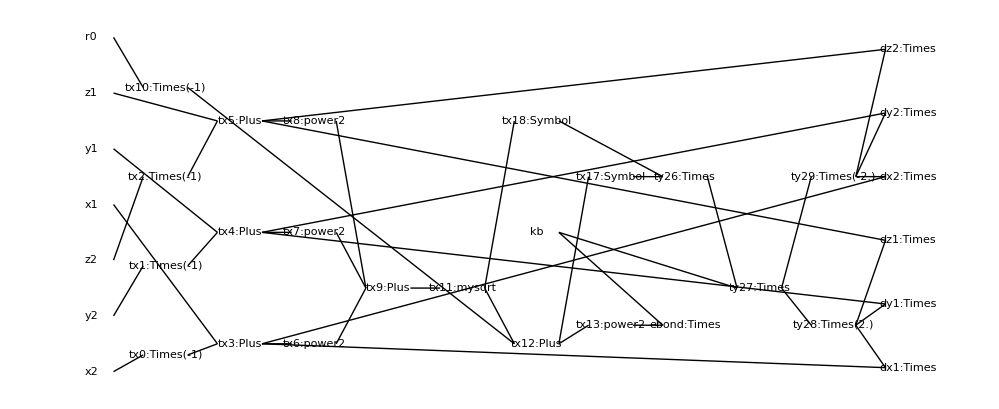

```mathematica
Show[Graphics[gr],AspectRatio->0.41]
```

## Bond stretch term using the chain rule and writing the energy in terms of the bond deviation

```mathematica
ba = { x1, y1, z1};
bb = { x2, y2, z2 };
```

```mathematica
fnEBond= bondK  (dev)^2
```

bondK dev^2

```mathematica
fnR = Sqrt[(ba-bb).(ba-bb)] -r0
```

-r0+√((x1-x2)^2+(y1-y2)^2+(z1-z2)^2)

```mathematica
names = Flatten[{ba,bb}]
```

{x1,y1,z1,x2,y2,z2}

```mathematica
trialBondValues[dist_] := Flatten[{
{v1->1, v2->2, v3->3},
{x1->1,y1->0,z1->0},
{x2->0,y2->0,z2->0},
{x3->0,y3->1,z3->0},
{x4->Cos[angle*0.0174533],y4->1,z4->Sin[angle*0.0174533]}
}]
```

```mathematica
be = {};
AppendTo[be,fnR->dev];
AppendTo[be,fnEBond->eBond];
```

AppendTo[be,firstDeriv[fnEBond,dev,fnR,x1]→gEBondx1];
AppendTo[be,firstDeriv[fnEBond,dev,fnR,y1]→gEBondy1];
AppendTo[be,firstDeriv[fnEBond,dev,fnR,z1]→gEBondz1];
AppendTo[be,-gEBondx1→gEBondx2];
AppendTo[be,-gEBondy1→gEBondy2];
AppendTo[be,-gEBondz1→gEBondz2];

```mathematica
gradient=buildGradient["gEBond",fnEBond,dev,fnR,names];AppendTo[be,gradient];
be=Flatten[be];
```

hessian = buildHessian["hEBond", fnEBond, dev, fnR, names];
AppendTo[be, hessian];
be = Flatten[be];

```mathematica
bondTerms = collectTermsForList[be,{}];
```

Collecting terms for equation: 1 dev

-x2→tx0

-y2→tx1

-z2→tx2

tx0+x1→tx3

tx1+y1→tx4

tx2+z1→tx5

tx3^2→tx6

tx4^2→tx7

tx5^2→tx8

tx6+tx7+tx8→tx9

-r0→tx10

√tx9→tx11

collected 12 terms

Collecting terms for equation: 2 eBond

dev^2→tx13

collected 1 terms

Collecting terms for equation: 3 gEBondx1

1/(√tx9)→tx15

collected 1 terms

Collecting terms for equation: 4 gEBondy1

Collecting terms for equation: 5 gEBondz1

Collecting terms for equation: 6 gEBondx2

Collecting terms for equation: 7 gEBondy2

Collecting terms for equation: 8 gEBondz2

```mathematica
Length[bondTerms]
```

22

```mathematica
simpleBondTermsB=simplifyProducts[bondTerms];
```

Substitute term: ty22=dev*tx15 at position:17 substitutions: 6

Substitute term: ty23=bondK*ty22 at position:18 substitutions: 6

Substitute term: ty24=2*ty23 at position:19 substitutions: 3

Substitute term: ty25=-2*ty23 at position:23 substitutions: 3

```mathematica
Length[simpleBondTermsB]
```

26

```mathematica
cFormListOfTerms[simpleBondTermsB]
```

double dev,eBond,gEBondx1,gEBondx2,gEBondy1,gEBondy2,gEBondz1,gEBondz2,tx0,tx1,tx10,tx11,tx13,tx15,tx2,tx3,tx4,tx5,tx6,tx7,tx8,tx9,ty22,ty23,ty24,ty25,xxxxDummy;
	tx0 = -x2; 		/* rule 1 */
	tx1 = -y2; 		/* rule 2 */
	tx2 = -z2; 		/* rule 3 */
	tx3 = tx0 + x1; 		/* rule 4 */
	tx4 = tx1 + y1; 		/* rule 5 */
	tx5 = tx2 + z1; 		/* rule 6 */
	tx6 = Power(tx3,2); 		/* rule 7 */
	tx7 = Power(tx4,2); 		/* rule 8 */
	tx8 = Power(tx5,2); 		/* rule 9 */
	tx9 = tx6 + tx7 + tx8; 		/* rule 10 */
	tx10 = -r0; 		/* rule 11 */
	tx11 = Sqrt(tx9); 		/* rule 12 */
	dev = tx10 + tx11; 		/* rule 13 */
	tx13 = Power(dev,2); 		/* rule 14 */
	eBond = bondK*tx13; 		/* rule 15 */
	tx15 = 1/Sqrt(tx9); 		/* rule 16 */
	ty22 = dev*tx15; 		/* rule 17 */
	ty23 = bondK*ty22; 		/* rule 18 */
	ty24 = 2*ty23; 		/* rule 19 */
	gEBondx1 = tx3*ty24; 		/* rule 20 */
	gEBondy1 = tx4*ty24; 		/* rule 21 */
	gEBondz1 = tx5*ty24; 		/* rule 22 */
	ty25 = -2*ty23; 		/* rule 23 */
	gEBondx2 = tx3*ty25; 		/* rule 24 */
	gEBondy2 = tx4*ty25; 		/* rule 25 */
	gEBondz2 = tx5*ty25; 		/* rule 26 */

## Angle bend term using simple minded gradient/Hessian expansion

```mathematica
Clear[x1,y1,z1,x2,y2,z2,x3,y3,z3,x,y,ba,bb,bc];
```

```mathematica
ba = { x1, y1, z1};
bb = { x2, y2, z2 };
bc = { x3, y3, z3 };
```

```mathematica
vecLen[a_] := Sqrt[Dot[a,a]];
```

```mathematica
x = ba - bb;
y = bc - bb;
fnThetaDev = ArcCos[Dot[x,y]/(vecLen[x] vecLen[y])]-t0
```

-t0+ArcCos[((x1-x2) (-x2+x3)+(y1-y2) (-y2+y3)+(z1-z2) (-z2+z3))/(√((x1-x2)^2+(y1-y2)^2+(z1-z2)^2) √((-x2+x3)^2+(-y2+y3)^2+(-z2+z3)^2))]

```mathematica
fnEAngle = angleK (thetaDev)^2
```

angleK thetaDev^2

```mathematica
fnEAngle = fnEAngle/.{thetaDev->fnThetaDev}
```

angleK (-t0+ArcCos[((x1-x2) (-x2+x3)+(y1-y2) (-y2+y3)+(z1-z2) (-z2+z3))/(√((x1-x2)^2+(y1-y2)^2+(z1-z2)^2) √((-x2+x3)^2+(-y2+y3)^2+(-z2+z3)^2))])^2

```mathematica
names = Flatten[Union[ba,bb,bc]]
```

{x1,x2,x3,y1,y2,y3,z1,z2,z3}

```mathematica
trialAngleValues[ang_] := Flatten[{
{angleK->100, t0->120*0.0174533},
{x1->1,y1->0,z1->0},
{x2->0,y2->0,z2->0},
{x3->Cos[ang*0.0174533],y3->Sin[ang*0.0174533],z3->0}
}]
```

### Energy

```mathematica
be = {fnEAngle->eangle};
```

### Gradient

```mathematica
For[i=1,i≤Length[names],i++,
AppendTo[be,D[fnEAngle,names[[i]]]->Symbol["d"<>ToString[names[[i]]]]];
];
```

### Hessian

For[i = 1, i <= Length[names], i++,
  For[j = i, j <= Length[names], j++, AppendTo[be, D[D[fnEAngle, names[[j]]], names[[i]]] -> Symbol["thEAngle" <> ToString[names[[j]]] <> ToString[names[[i]]]]];
    ];
  ];

### Collect and simplify

```mathematica
Length[be]
```

10

```mathematica
angleTerms0 = collectTermsForList[be,{}]/.simplifyRules;
```

Collecting terms for equation: 1 eangle

-x2→tx0

-y2→tx1

-z2→tx2

tx0+x1→tx3

tx0+x3→tx4

tx1+y1→tx5

tx1+y3→tx6

tx2+z1→tx7

tx2+z3→tx8

tx3^2→tx9

tx4^2→tx10

tx5^2→tx11

tx6^2→tx12

tx7^2→tx13

tx8^2→tx14

tx10+tx12+tx14→tx15

tx3 tx4→tx16

tx5 tx6→tx17

tx7 tx8→tx18

tx11+tx13+tx9→tx19

1/(√tx15)→tx20

tx16+tx17+tx18→tx21

1/(√tx19)→tx22

tx20 tx21 tx22→tx23

-t0→tx24

ArcCos[tx23]→tx25

tx24+tx25→tx26

tx26^2→tx27

collected 28 terms

Collecting terms for equation: 2 dx1

1/tx15→tx29

1/tx19→tx30

tx21^2→tx31

1/tx19^(3/2)→tx32

-tx29 tx30 tx31→tx33

-tx20 tx21 tx3 tx32→tx34

1+tx33→tx35

tx20 tx22 tx4→tx36

1/(√tx35)→tx37

tx34+tx36→tx38

collected 10 terms

Collecting terms for equation: 3 dx2

-x1→tx40

2 x2→tx41

-x3→tx42

1/tx15^(3/2)→tx43

tx40+tx41+tx42→tx44

tx20 tx21 tx3 tx32→tx45

tx21 tx22 tx4 tx43→tx46

tx20 tx22 tx44→tx47

tx45+tx46+tx47→tx48

collected 9 terms

Collecting terms for equation: 4 dx3

tx20 tx22 tx3→tx50

-tx46→tx51

tx50+tx51→tx52

collected 3 terms

Collecting terms for equation: 5 dy1

-tx20 tx21 tx32 tx5→tx54

tx20 tx22 tx6→tx55

tx54+tx55→tx56

collected 3 terms

Collecting terms for equation: 6 dy2

-y1→tx58

2 y2→tx59

-y3→tx60

tx58+tx59+tx60→tx61

tx20 tx21 tx32 tx5→tx62

tx21 tx22 tx43 tx6→tx63

tx20 tx22 tx61→tx64

tx62+tx63+tx64→tx65

collected 8 terms

Collecting terms for equation: 7 dy3

tx20 tx22 tx5→tx67

-tx63→tx68

tx67+tx68→tx69

collected 3 terms

Collecting terms for equation: 8 dz1

-tx20 tx21 tx32 tx7→tx71

tx20 tx22 tx8→tx72

tx71+tx72→tx73

collected 3 terms

Collecting terms for equation: 9 dz2

-z1→tx75

2 z2→tx76

-z3→tx77

tx75+tx76+tx77→tx78

tx20 tx21 tx32 tx7→tx79

tx20 tx22 tx78→tx80

tx21 tx22 tx43 tx8→tx81

tx79+tx80+tx81→tx82

collected 8 terms

Collecting terms for equation: 10 dz3

tx20 tx22 tx7→tx84

-tx81→tx85

tx84+tx85→tx86

collected 3 terms

```mathematica
Length[angleTerms0]
```

88

```mathematica
ccode = cFormListOfTerms[angleTerms0];
```

```mathematica
angleTerms = collectTermsForList[angleTerms0,{}]/.simplifyRules;
```

Collecting terms for equation: 1 tx0

Collecting terms for equation: 2 tx1

Collecting terms for equation: 3 tx2

Collecting terms for equation: 4 tx3

Collecting terms for equation: 5 tx4

Collecting terms for equation: 6 tx5

Collecting terms for equation: 7 tx6

Collecting terms for equation: 8 tx7

Collecting terms for equation: 9 tx8

Collecting terms for equation: 10 tx9

Collecting terms for equation: 11 tx10

Collecting terms for equation: 12 tx11

Collecting terms for equation: 13 tx12

Collecting terms for equation: 14 tx13

Collecting terms for equation: 15 tx14

Collecting terms for equation: 16 tx15

Collecting terms for equation: 17 tx16

Collecting terms for equation: 18 tx17

Collecting terms for equation: 19 tx18

Collecting terms for equation: 20 tx19

Collecting terms for equation: 21 tx20

Collecting terms for equation: 22 tx21

Collecting terms for equation: 23 tx22

Collecting terms for equation: 24 tx23

Collecting terms for equation: 25 tx24

Collecting terms for equation: 26 tx25

Collecting terms for equation: 27 tx26

Collecting terms for equation: 28 tx27

Collecting terms for equation: 29 eangle

Collecting terms for equation: 30 tx29

Collecting terms for equation: 31 tx30

Collecting terms for equation: 32 tx31

Collecting terms for equation: 33 tx32

power1[tx19]→tx32

1/tx22→tx33

1/tx32→tx34

collected 3 terms

Collecting terms for equation: 34 tx33

Collecting terms for equation: 35 tx34

Collecting terms for equation: 36 tx35

Collecting terms for equation: 37 tx36

Collecting terms for equation: 38 tx37

Collecting terms for equation: 39 tx38

Collecting terms for equation: 40 dx1

Collecting terms for equation: 41 tx40

Collecting terms for equation: 42 tx41

Collecting terms for equation: 43 tx42

Collecting terms for equation: 44 tx43

power1[tx15]→tx46

1/tx20→tx47

1/tx46→tx48

collected 3 terms

Collecting terms for equation: 45 tx44

Collecting terms for equation: 46 tx45

Collecting terms for equation: 47 tx46

Collecting terms for equation: 48 tx47

Collecting terms for equation: 49 tx48

Collecting terms for equation: 50 dx2

Collecting terms for equation: 51 tx50

Collecting terms for equation: 52 tx51

Collecting terms for equation: 53 tx52

Collecting terms for equation: 54 dx3

Collecting terms for equation: 55 tx54

Collecting terms for equation: 56 tx55

Collecting terms for equation: 57 tx56

Collecting terms for equation: 58 dy1

Collecting terms for equation: 59 tx58

Collecting terms for equation: 60 tx59

Collecting terms for equation: 61 tx60

Collecting terms for equation: 62 tx61

Collecting terms for equation: 63 tx62

Collecting terms for equation: 64 tx63

Collecting terms for equation: 65 tx64

Collecting terms for equation: 66 tx65

Collecting terms for equation: 67 dy2

Collecting terms for equation: 68 tx67

Collecting terms for equation: 69 tx68

Collecting terms for equation: 70 tx69

Collecting terms for equation: 71 dy3

Collecting terms for equation: 72 tx71

Collecting terms for equation: 73 tx72

Collecting terms for equation: 74 tx73

Collecting terms for equation: 75 dz1

Collecting terms for equation: 76 tx75

Collecting terms for equation: 77 tx76

Collecting terms for equation: 78 tx77

Collecting terms for equation: 79 tx78

Collecting terms for equation: 80 tx79

Collecting terms for equation: 81 tx80

Collecting terms for equation: 82 tx81

Collecting terms for equation: 83 tx82

Collecting terms for equation: 84 dz2

Collecting terms for equation: 85 tx84

Collecting terms for equation: 86 tx85

Collecting terms for equation: 87 tx86

Collecting terms for equation: 88 dz3

```mathematica
Length[angleTerms]
```

94

```mathematica
simpleAngleTermsA=simplifyProducts[angleTerms];
```

Substitute term: ty94=tx20*tx22 at position:24 substitutions: 10

Substitute term: ty95=tx26*tx37 at position:44 substitutions: 9

Substitute term: ty96=angleK*ty95 at position:45 substitutions: 9

Substitute term: ty97=-2*ty96 at position:46 substitutions: 9

Substitute term: ty98=tx21*tx32 at position:39 substitutions: 6

Substitute term: ty99=tx20*ty98 at position:40 substitutions: 6

Substitute term: ty100=tx22*tx43 at position:59 substitutions: 3

Substitute term: ty101=tx21*ty100 at position:60 substitutions: 3

Substitute term: ty102=-ty99 at position:41 substitutions: 3

```mathematica
ccode = cFormListOfTerms[simpleAngleTermsA]
```

double dx1,dx2,dx3,dy1,dy2,dy3,dz1,dz2,dz3,eangle,tx0,tx1,tx10,tx11,tx12,tx13,tx14,tx15,tx16,tx17,tx18,tx19,tx2,tx20,tx21,tx22,tx23,tx24,tx25,tx26,tx27,tx29,tx3,tx30,tx31,tx32,tx33,tx34,tx35,tx36,tx37,tx38,tx4,tx40,tx41,tx42,tx43,tx44,tx45,tx46,tx47,tx48,tx5,tx50,tx51,tx52,tx54,tx55,tx56,tx58,tx59,tx6,tx60,tx61,tx62,tx63,tx64,tx65,tx67,tx68,tx69,tx7,tx71,tx72,tx73,tx75,tx76,tx77,tx78,tx79,tx8,tx80,tx81,tx82,tx84,tx85,tx86,tx9,ty100,ty101,ty102,ty94,ty95,ty96,ty97,ty98,ty99,xxxxDummy;
	tx0 = -x2; 		/* rule 1 */
	tx1 = -y2; 		/* rule 2 */
	tx2 = -z2; 		/* rule 3 */
	tx3 = tx0 + x1; 		/* rule 4 */
	tx4 = tx0 + x3; 		/* rule 5 */
	tx5 = tx1 + y1; 		/* rule 6 */
	tx6 = tx1 + y3; 		/* rule 7 */
	tx7 = tx2 + z1; 		/* rule 8 */
	tx8 = tx2 + z3; 		/* rule 9 */
	tx9 = power2(tx3); 		/* rule 10 */
	tx10 = power2(tx4); 		/* rule 11 */
	tx11 = power2(tx5); 		/* rule 12 */
	tx12 = power2(tx6); 		/* rule 13 */
	tx13 = power2(tx7); 		/* rule 14 */
	tx14 = power2(tx8); 		/* rule 15 */
	tx15 = tx10 + tx12 + tx14; 		/* rule 16 */
	tx16 = tx3*tx4; 		/* rule 17 */
	tx17 = tx5*tx6; 		/* rule 18 */
	tx18 = tx7*tx8; 		/* rule 19 */
	tx19 = tx11 + tx13 + tx9; 		/* rule 20 */
	tx20 = mysqrt(tx15); 		/* rule 21 */
	tx21 = tx16 + tx17 + tx18; 		/* rule 22 */
	tx22 = mysqrt(tx19); 		/* rule 23 */
	ty94 = tx20*tx22; 		/* rule 24 */
	tx23 = tx21*ty94; 		/* rule 25 */
	tx24 = -t0; 		/* rule 26 */
	tx25 = ArcCos(tx23); 		/* rule 27 */
	tx26 = tx24 + tx25; 		/* rule 28 */
	tx27 = power2(tx26); 		/* rule 29 */
	eangle = angleK*tx27; 		/* rule 30 */
	tx29 = powern1(tx15); 		/* rule 31 */
	tx30 = powern1(tx19); 		/* rule 32 */
	tx31 = power2(tx21); 		/* rule 33 */
	tx32 = power1(tx19); 		/* rule 34 */
	tx33 = powern1(tx22); 		/* rule 35 */
	tx34 = powern1(tx32); 		/* rule 36 */
	tx32 = tx33*tx34; 		/* rule 37 */
	tx33 = -(tx29*tx30*tx31); 		/* rule 38 */
	ty98 = tx21*tx32; 		/* rule 39 */
	ty99 = tx20*ty98; 		/* rule 40 */
	ty102 = -ty99; 		/* rule 41 */
	tx34 = tx3*ty102; 		/* rule 42 */
	tx35 = 1 + tx33; 		/* rule 43 */
	tx36 = tx4*ty94; 		/* rule 44 */
	tx37 = mysqrt(tx35); 		/* rule 45 */
	tx38 = tx34 + tx36; 		/* rule 46 */
	ty95 = tx26*tx37; 		/* rule 47 */
	ty96 = angleK*ty95; 		/* rule 48 */
	ty97 = -2*ty96; 		/* rule 49 */
	dx1 = tx38*ty97; 		/* rule 50 */
	tx40 = -x1; 		/* rule 51 */
	tx41 = 2*x2; 		/* rule 52 */
	tx42 = -x3; 		/* rule 53 */
	tx46 = power1(tx15); 		/* rule 54 */
	tx47 = powern1(tx20); 		/* rule 55 */
	tx48 = powern1(tx46); 		/* rule 56 */
	tx43 = tx47*tx48; 		/* rule 57 */
	tx44 = tx40 + tx41 + tx42; 		/* rule 58 */
	tx45 = tx3*ty99; 		/* rule 59 */
	ty100 = tx22*tx43; 		/* rule 60 */
	ty101 = tx21*ty100; 		/* rule 61 */
	tx46 = tx4*ty101; 		/* rule 62 */
	tx47 = tx44*ty94; 		/* rule 63 */
	tx48 = tx45 + tx46 + tx47; 		/* rule 64 */
	dx2 = tx48*ty97; 		/* rule 65 */
	tx50 = tx3*ty94; 		/* rule 66 */
	tx51 = -tx46; 		/* rule 67 */
	tx52 = tx50 + tx51; 		/* rule 68 */
	dx3 = tx52*ty97; 		/* rule 69 */
	tx54 = tx5*ty102; 		/* rule 70 */
	tx55 = tx6*ty94; 		/* rule 71 */
	tx56 = tx54 + tx55; 		/* rule 72 */
	dy1 = tx56*ty97; 		/* rule 73 */
	tx58 = -y1; 		/* rule 74 */
	tx59 = 2*y2; 		/* rule 75 */
	tx60 = -y3; 		/* rule 76 */
	tx61 = tx58 + tx59 + tx60; 		/* rule 77 */
	tx62 = tx5*ty99; 		/* rule 78 */
	tx63 = tx6*ty101; 		/* rule 79 */
	tx64 = tx61*ty94; 		/* rule 80 */
	tx65 = tx62 + tx63 + tx64; 		/* rule 81 */
	dy2 = tx65*ty97; 		/* rule 82 */
	tx67 = tx5*ty94; 		/* rule 83 */
	tx68 = -tx63; 		/* rule 84 */
	tx69 = tx67 + tx68; 		/* rule 85 */
	dy3 = tx69*ty97; 		/* rule 86 */
	tx71 = tx7*ty102; 		/* rule 87 */
	tx72 = tx8*ty94; 		/* rule 88 */
	tx73 = tx71 + tx72; 		/* rule 89 */
	dz1 = tx73*ty97; 		/* rule 90 */
	tx75 = -z1; 		/* rule 91 */
	tx76 = 2*z2; 		/* rule 92 */
	tx77 = -z3; 		/* rule 93 */
	tx78 = tx75 + tx76 + tx77; 		/* rule 94 */
	tx79 = tx7*ty99; 		/* rule 95 */
	tx80 = tx78*ty94; 		/* rule 96 */
	tx81 = tx8*ty101; 		/* rule 97 */
	tx82 = tx79 + tx80 + tx81; 		/* rule 98 */
	dz2 = tx82*ty97; 		/* rule 99 */
	tx84 = tx7*ty94; 		/* rule 100 */
	tx85 = -tx81; 		/* rule 101 */
	tx86 = tx84 + tx85; 		/* rule 102 */
	dz3 = tx86*ty97; 		/* rule 103 */

```mathematica
s = OpenWrite["angleTerms.cc"];
Write[s,ccode];
Close[s];
```

```mathematica
simpleAngleTermsA[[57]]//FullForm
```

Rule[Times[tx47,tx48],tx43]

```mathematica
simpleAngleTermsA[[21]]//FullForm
```

Rule[mysqrt[tx15],tx20]

```mathematica
simpleAngleTermsA[[34]]/.simplifyRules//FullForm
```

Rule[power1[tx19],tx32]

```mathematica
Length[simpleAngleTermsA]
```

103

trial = trialAngleValues[130]

expTest = selectRules[be /. trial]

```mathematica
.10createEntireTree[simpleAngleTermsA]
```

.10createEntireTree[{-x2→tx0,-y2→tx1,-z2→tx2,tx0+x1→tx3,tx0+x3→tx4,tx1+y1→tx5,tx1+y3→tx6,tx2+z1→tx7,tx2+z3→tx8,power2[tx3]→tx9,power2[tx4]→tx10,power2[tx5]→tx11,power2[tx6]→tx12,power2[tx7]→tx13,power2[tx8]→tx14,tx10+tx12+tx14→tx15,tx3 tx4→tx16,tx5 tx6→tx17,tx7 tx8→tx18,tx11+tx13+tx9→tx19,mysqrt[tx15]→tx20,tx16+tx17+tx18→tx21,mysqrt[tx19]→tx22,tx20 tx22→ty94,tx21 ty94→tx23,-t0→tx24,ArcCos[tx23]→tx25,tx24+tx25→tx26,power2[tx26]→tx27,angleK tx27→eangle,powern1[tx15]→tx29,powern1[tx19]→tx30,power2[tx21]→tx31,power1[tx19]→tx32,powern1[tx22]→tx33,powern1[tx32]→tx34,tx33 tx34→tx32,-tx29 tx30 tx31→tx33,tx21 tx32→ty98,tx20 ty98→ty99,-ty99→ty102,tx3 ty102→tx34,1+tx33→tx35,tx4 ty94→tx36,mysqrt[tx35]→tx37,tx34+tx36→tx38,tx26 tx37→ty95,angleK ty95→ty96,-2 ty96→ty97,tx38 ty97→dx1,-x1→tx40,2 x2→tx41,-x3→tx42,power1[tx15]→tx46,powern1[tx20]→tx47,powern1[tx46]→tx48,tx47 tx48→tx43,tx40+tx41+tx42→tx44,tx3 ty99→tx45,tx22 tx43→ty100,tx21 ty100→ty101,tx4 ty101→tx46,tx44 ty94→tx47,tx45+tx46+tx47→tx48,tx48 ty97→dx2,tx3 ty94→tx50,-tx46→tx51,tx50+tx51→tx52,tx52 ty97→dx3,tx5 ty102→tx54,tx6 ty94→tx55,tx54+tx55→tx56,tx56 ty97→dy1,-y1→tx58,2 y2→tx59,-y3→tx60,tx58+tx59+tx60→tx61,tx5 ty99→tx62,tx6 ty101→tx63,tx61 ty94→tx64,tx62+tx63+tx64→tx65,tx65 ty97→dy2,tx5 ty94→tx67,-tx63→tx68,tx67+tx68→tx69,tx69 ty97→dy3,tx7 ty102→tx71,tx8 ty94→tx72,tx71+tx72→tx73,tx73 ty97→dz1,-z1→tx75,2 z2→tx76,-z3→tx77,tx75+tx76+tx77→tx78,tx7 ty99→tx79,tx78 ty94→tx80,tx8 ty101→tx81,tx79+tx80+tx81→tx82,tx82 ty97→dz2,tx7 ty94→tx84,-tx81→tx85,tx84+tx85→tx86,tx86 ty97→dz3}]

```mathematica
gr = buildTreeGraphics[20,20];
```

```mathematica
gr[[2]]
```

Line[{{14.,16.7347},{6.,189.231}}]

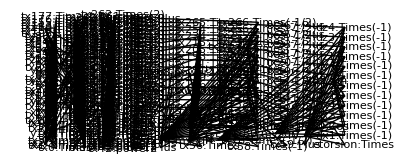

```mathematica
Show[Graphics[gr],AspectRatio->0.41]
```

```mathematica
Export["c:\\angle.eps",Graphics[gr],"EPS"]
```

c:\angle.eps

## Angle bend term using the chain rule expansion

```mathematica
Clear[x,y,ba,bb,bc];
```

```mathematica
ba = { x1, y1, z1};
bb = { x2, y2, z2 };
bc = { x3, y3, z3 };
```

```mathematica
vecLen[a_] := Sqrt[Dot[a,a]];
```

```mathematica
x = ba - bb;
y = bc - bb;
fnThetaDev = ArcCos[Dot[x,y]/(vecLen[x] vecLen[y])]-t0
```

-t0+ArcCos[((x1-x2) (-x2+x3)+(y1-y2) (-y2+y3)+(z1-z2) (-z2+z3))/(√((x1-x2)^2+(y1-y2)^2+(z1-z2)^2) √((-x2+x3)^2+(-y2+y3)^2+(-z2+z3)^2))]

```mathematica
fnEAngle = angleK (thetaDev)^2
```

angleK thetaDev^2

```mathematica
names = Flatten[Union[ba,bb,bc]]
```

{x1,x2,x3,y1,y2,y3,z1,z2,z3}

```mathematica
be = {};
AppendTo[be,fnThetaDev->thetaDev];
AppendTo[be,fnEAngle->eangle];
```

```mathematica
gradient = buildGradient["d",fnEAngle,thetaDev,fnThetaDev,names];AppendTo[be,gradient];
be = Flatten[be];
```

hessian = buildHessian["hEAngle", fnEAngle, thetaDev, fnThetaDev, names];
AppendTo[be, hessian];
be = Flatten[be];

```mathematica
angleTerms = collectTermsForList[be,{}];
```

Collecting terms for equation: 1 thetaDev

-x2→tx0

-y2→tx1

-z2→tx2

tx0+x1→tx3

tx0+x3→tx4

tx1+y1→tx5

tx1+y3→tx6

tx2+z1→tx7

tx2+z3→tx8

tx3^2→tx9

tx4^2→tx10

tx5^2→tx11

tx6^2→tx12

tx7^2→tx13

tx8^2→tx14

tx10+tx12+tx14→tx15

tx3 tx4→tx16

tx5 tx6→tx17

tx7 tx8→tx18

tx11+tx13+tx9→tx19

1/(√tx15)→tx20

tx16+tx17+tx18→tx21

1/(√tx19)→tx22

tx20 tx21 tx22→tx23

-t0→tx24

ArcCos[tx23]→tx25

collected 26 terms

Collecting terms for equation: 2 eangle

thetaDev^2→tx27

collected 1 terms

Collecting terms for equation: 3 dx1

1/tx15→tx29

1/tx19→tx30

tx21^2→tx31

1/tx19^(3/2)→tx32

-tx29 tx30 tx31→tx33

-tx20 tx21 tx3 tx32→tx34

1+tx33→tx35

tx20 tx22 tx4→tx36

1/(√tx35)→tx37

tx34+tx36→tx38

collected 10 terms

Collecting terms for equation: 4 dx2

-x1→tx40

2 x2→tx41

-x3→tx42

1/tx15^(3/2)→tx43

tx40+tx41+tx42→tx44

tx20 tx21 tx3 tx32→tx45

tx21 tx22 tx4 tx43→tx46

tx20 tx22 tx44→tx47

tx45+tx46+tx47→tx48

collected 9 terms

Collecting terms for equation: 5 dx3

tx20 tx22 tx3→tx50

-tx46→tx51

tx50+tx51→tx52

collected 3 terms

Collecting terms for equation: 6 dy1

-tx20 tx21 tx32 tx5→tx54

tx20 tx22 tx6→tx55

tx54+tx55→tx56

collected 3 terms

Collecting terms for equation: 7 dy2

-y1→tx58

2 y2→tx59

-y3→tx60

tx58+tx59+tx60→tx61

tx20 tx21 tx32 tx5→tx62

tx21 tx22 tx43 tx6→tx63

tx20 tx22 tx61→tx64

tx62+tx63+tx64→tx65

collected 8 terms

Collecting terms for equation: 8 dy3

tx20 tx22 tx5→tx67

-tx63→tx68

tx67+tx68→tx69

collected 3 terms

Collecting terms for equation: 9 dz1

-tx20 tx21 tx32 tx7→tx71

tx20 tx22 tx8→tx72

tx71+tx72→tx73

collected 3 terms

Collecting terms for equation: 10 dz2

-z1→tx75

2 z2→tx76

-z3→tx77

tx75+tx76+tx77→tx78

tx20 tx21 tx32 tx7→tx79

tx20 tx22 tx78→tx80

tx21 tx22 tx43 tx8→tx81

tx79+tx80+tx81→tx82

collected 8 terms

Collecting terms for equation: 11 dz3

tx20 tx22 tx7→tx84

-tx81→tx85

tx84+tx85→tx86

collected 3 terms

```mathematica
Length[angleTerms]
```

88

```mathematica
simpleAngleTermsB=simplifyProducts[angleTerms];
```

Substitute term: ty88=tx20*tx22 at position:24 substitutions: 10

Substitute term: ty89=thetaDev*tx37 at position:41 substitutions: 9

Substitute term: ty90=angleK*ty89 at position:42 substitutions: 9

Substitute term: ty91=-2*ty90 at position:43 substitutions: 9

Substitute term: ty92=tx21*tx32 at position:36 substitutions: 6

Substitute term: ty93=tx20*ty92 at position:37 substitutions: 6

Substitute term: ty94=tx22*tx43 at position:53 substitutions: 3

Substitute term: ty95=tx21*ty94 at position:54 substitutions: 3

Substitute term: ty96=-ty93 at position:38 substitutions: 3

```mathematica
cFormListOfTerms[simpleAngleTermsB]
```

double dx1,dx2,dx3,dy1,dy2,dy3,dz1,dz2,dz3,eangle,thetaDev,tx0,tx1,tx10,tx11,tx12,tx13,tx14,tx15,tx16,tx17,tx18,tx19,tx2,tx20,tx21,tx22,tx23,tx24,tx25,tx27,tx29,tx3,tx30,tx31,tx32,tx33,tx34,tx35,tx36,tx37,tx38,tx4,tx40,tx41,tx42,tx43,tx44,tx45,tx46,tx47,tx48,tx5,tx50,tx51,tx52,tx54,tx55,tx56,tx58,tx59,tx6,tx60,tx61,tx62,tx63,tx64,tx65,tx67,tx68,tx69,tx7,tx71,tx72,tx73,tx75,tx76,tx77,tx78,tx79,tx8,tx80,tx81,tx82,tx84,tx85,tx86,tx9,ty88,ty89,ty90,ty91,ty92,ty93,ty94,ty95,ty96,xxxxDummy;
	tx0 = -x2; 		/* rule 1 */
	tx1 = -y2; 		/* rule 2 */
	tx2 = -z2; 		/* rule 3 */
	tx3 = tx0 + x1; 		/* rule 4 */
	tx4 = tx0 + x3; 		/* rule 5 */
	tx5 = tx1 + y1; 		/* rule 6 */
	tx6 = tx1 + y3; 		/* rule 7 */
	tx7 = tx2 + z1; 		/* rule 8 */
	tx8 = tx2 + z3; 		/* rule 9 */
	tx9 = Power(tx3,2); 		/* rule 10 */
	tx10 = Power(tx4,2); 		/* rule 11 */
	tx11 = Power(tx5,2); 		/* rule 12 */
	tx12 = Power(tx6,2); 		/* rule 13 */
	tx13 = Power(tx7,2); 		/* rule 14 */
	tx14 = Power(tx8,2); 		/* rule 15 */
	tx15 = tx10 + tx12 + tx14; 		/* rule 16 */
	tx16 = tx3*tx4; 		/* rule 17 */
	tx17 = tx5*tx6; 		/* rule 18 */
	tx18 = tx7*tx8; 		/* rule 19 */
	tx19 = tx11 + tx13 + tx9; 		/* rule 20 */
	tx20 = 1/Sqrt(tx15); 		/* rule 21 */
	tx21 = tx16 + tx17 + tx18; 		/* rule 22 */
	tx22 = 1/Sqrt(tx19); 		/* rule 23 */
	ty88 = tx20*tx22; 		/* rule 24 */
	tx23 = tx21*ty88; 		/* rule 25 */
	tx24 = -t0; 		/* rule 26 */
	tx25 = ArcCos(tx23); 		/* rule 27 */
	thetaDev = tx24 + tx25; 		/* rule 28 */
	tx27 = Power(thetaDev,2); 		/* rule 29 */
	eangle = angleK*tx27; 		/* rule 30 */
	tx29 = 1/tx15; 		/* rule 31 */
	tx30 = 1/tx19; 		/* rule 32 */
	tx31 = Power(tx21,2); 		/* rule 33 */
	tx32 = Power(tx19,-1.5); 		/* rule 34 */
	tx33 = -(tx29*tx30*tx31); 		/* rule 35 */
	ty92 = tx21*tx32; 		/* rule 36 */
	ty93 = tx20*ty92; 		/* rule 37 */
	ty96 = -ty93; 		/* rule 38 */
	tx34 = tx3*ty96; 		/* rule 39 */
	tx35 = 1 + tx33; 		/* rule 40 */
	tx36 = tx4*ty88; 		/* rule 41 */
	tx37 = 1/Sqrt(tx35); 		/* rule 42 */
	tx38 = tx34 + tx36; 		/* rule 43 */
	ty89 = thetaDev*tx37; 		/* rule 44 */
	ty90 = angleK*ty89; 		/* rule 45 */
	ty91 = -2*ty90; 		/* rule 46 */
	dx1 = tx38*ty91; 		/* rule 47 */
	tx40 = -x1; 		/* rule 48 */
	tx41 = 2*x2; 		/* rule 49 */
	tx42 = -x3; 		/* rule 50 */
	tx43 = Power(tx15,-1.5); 		/* rule 51 */
	tx44 = tx40 + tx41 + tx42; 		/* rule 52 */
	tx45 = tx3*ty93; 		/* rule 53 */
	ty94 = tx22*tx43; 		/* rule 54 */
	ty95 = tx21*ty94; 		/* rule 55 */
	tx46 = tx4*ty95; 		/* rule 56 */
	tx47 = tx44*ty88; 		/* rule 57 */
	tx48 = tx45 + tx46 + tx47; 		/* rule 58 */
	dx2 = tx48*ty91; 		/* rule 59 */
	tx50 = tx3*ty88; 		/* rule 60 */
	tx51 = -tx46; 		/* rule 61 */
	tx52 = tx50 + tx51; 		/* rule 62 */
	dx3 = tx52*ty91; 		/* rule 63 */
	tx54 = tx5*ty96; 		/* rule 64 */
	tx55 = tx6*ty88; 		/* rule 65 */
	tx56 = tx54 + tx55; 		/* rule 66 */
	dy1 = tx56*ty91; 		/* rule 67 */
	tx58 = -y1; 		/* rule 68 */
	tx59 = 2*y2; 		/* rule 69 */
	tx60 = -y3; 		/* rule 70 */
	tx61 = tx58 + tx59 + tx60; 		/* rule 71 */
	tx62 = tx5*ty93; 		/* rule 72 */
	tx63 = tx6*ty95; 		/* rule 73 */
	tx64 = tx61*ty88; 		/* rule 74 */
	tx65 = tx62 + tx63 + tx64; 		/* rule 75 */
	dy2 = tx65*ty91; 		/* rule 76 */
	tx67 = tx5*ty88; 		/* rule 77 */
	tx68 = -tx63; 		/* rule 78 */
	tx69 = tx67 + tx68; 		/* rule 79 */
	dy3 = tx69*ty91; 		/* rule 80 */
	tx71 = tx7*ty96; 		/* rule 81 */
	tx72 = tx8*ty88; 		/* rule 82 */
	tx73 = tx71 + tx72; 		/* rule 83 */
	dz1 = tx73*ty91; 		/* rule 84 */
	tx75 = -z1; 		/* rule 85 */
	tx76 = 2*z2; 		/* rule 86 */
	tx77 = -z3; 		/* rule 87 */
	tx78 = tx75 + tx76 + tx77; 		/* rule 88 */
	tx79 = tx7*ty93; 		/* rule 89 */
	tx80 = tx78*ty88; 		/* rule 90 */
	tx81 = tx8*ty95; 		/* rule 91 */
	tx82 = tx79 + tx80 + tx81; 		/* rule 92 */
	dz2 = tx82*ty91; 		/* rule 93 */
	tx84 = tx7*ty88; 		/* rule 94 */
	tx85 = -tx81; 		/* rule 95 */
	tx86 = tx84 + tx85; 		/* rule 96 */
	dz3 = tx86*ty91; 		/* rule 97 */

```mathematica
Length[simpleAngleTermsB]
```

97

## Torsion term using simple minded gradient/Hessian expansion

```mathematica
Clear[x1,y1,z1,x2,y2,z2,x3,y3,z3,x4,y4,z4];
```

```mathematica
ba = { x1, y1, z1};
bb = { x2, y2, z2 };
bc = { x3, y3, z3 };
bd = {x4, y4, z4};
```

```mathematica
vecLen[a_] := Sqrt[Dot[a,a]];
```

```mathematica
vF = ba - bb;
vG = bc - bb;
vH = bd - bc;
vA = Cross[vF,vG];
vB = Cross[vG,vH];
```

```mathematica
fnPhiDev = ArcCos[Dot[vA,vB]/(vecLen[vA] vecLen[vB])];
```

```mathematica
fnETorsionPart = V Cos[N phi-phase]
```

V Cos[phase-N phi]

```mathematica
fnETorsion = fnETorsionPart/.{phi->fnPhiDev};
```

```mathematica
names = Flatten[Union[ba,bb,bc,bd]]
```

{x1,x2,x3,x4,y1,y2,y3,y4,z1,z2,z3,z4}

```mathematica
trialTorsionValues[angle_] := Flatten[{
{v1->1, v2->2, v3->3},
{x1->1,y1->0,z1->0},
{x2->0,y2->0,z2->0},
{x3->0,y3->1,z3->0},
{x4->Cos[angle*0.0174533],y4->1,z4->Sin[angle*0.0174533]}
}]
```

### Energy

```mathematica
be = {fnETorsion->etorsion};
```

### Gradient

```mathematica
For[i=1,i≤Length[names],i++,
sym = Symbol["d"<>ToString[names[[i]]]];
AppendTo[be,D[fnETorsion,names[[i]]]->sym];
];
```

### Hessian

For[i = 1, i <= Length[names], i++, For[j = i, j <= Length[names], j++,
    sym = Symbol["thETorsion" <> ToString[names[[j]]] <> ToString[names[[i]]]];
    (*Print["Calculating expression", sym];*)
    AppendTo[be, D[D[fnETorsion, names[[j]]], names[[i]]] -> sym];
    ];
  ];

```mathematica
Length[be]
```

13

```mathematica
torsionTerms0 = collectTermsForList[be,{}]/.simplifyRules;
```

Collecting terms for equation: 1 etorsion

x2 y1→tx0

-x3 y1→tx1

-x1 y2→tx2

-x3 y2→tx3

x3 y2→tx4

x4 y2→tx5

x1 y3→tx6

-x2 y3→tx7

x2 y3→tx8

-x4 y3→tx9

-x2 y4→tx10

x3 y4→tx11

-x2 z1→tx12

x3 z1→tx13

y2 z1→tx14

-y3 z1→tx15

x1 z2→tx16

-x3 z2→tx17

x3 z2→tx18

-x4 z2→tx19

-y1 z2→tx20

-y3 z2→tx21

y3 z2→tx22

y4 z2→tx23

-x1 z3→tx24

-x2 z3→tx25

x2 z3→tx26

x4 z3→tx27

y1 z3→tx28

-y2 z3→tx29

y2 z3→tx30

-y4 z3→tx31

x2 z4→tx32

-x3 z4→tx33

-y2 z4→tx34

y3 z4→tx35

tx12+tx13+tx16+tx17+tx24+tx26→tx36

tx14+tx15+tx20+tx22+tx28+tx29→tx37

tx18+tx19+tx25+tx27+tx32+tx33→tx38

tx21+tx23+tx30+tx31+tx34+tx35→tx39

tx0+tx1+tx2+tx4+tx6+tx7→tx40

tx10+tx11+tx3+tx5+tx8+tx9→tx41

tx36^2→tx42

tx37^2→tx43

tx38^2→tx44

tx39^2→tx45

tx40^2→tx46

tx41^2→tx47

tx36 tx38→tx48

tx37 tx39→tx49

tx40 tx41→tx50

tx42+tx43+tx46→tx51

tx44+tx45+tx47→tx52

tx48+tx49+tx50→tx53

1/(√tx51)→tx54

1/(√tx52)→tx55

tx53 tx54 tx55→tx56

ArcCos[tx56]→tx57

-N tx57→tx58

phase+tx58→tx59

Cos[tx59]→tx60

collected 61 terms

Collecting terms for equation: 2 dx1

-y2→tx62

-z3→tx63

tx62+y3→tx64

tx63+z2→tx65

1/tx51→tx66

1/tx52→tx67

tx53^2→tx68

2 tx40 tx64→tx69

tx41 tx64→tx70

2 tx36 tx65→tx71

tx38 tx65→tx72

1/tx51^(3/2)→tx73

-tx66 tx67 tx68→tx74

tx69+tx71→tx75

tx70+tx72→tx76

1+tx74→tx77

-1/2 tx53 tx55 tx73 tx75→tx78

tx54 tx55 tx76→tx79

1/(√tx77)→tx80

tx78+tx79→tx81

Sin[tx59]→tx82

collected 21 terms

Collecting terms for equation: 3 dx2

-y3→tx84

-y4→tx85

-z1→tx86

tx84+y1→tx87

tx85+y3→tx88

tx86+z3→tx89

tx63+z4→tx90

2 tx40 tx87→tx91

tx41 tx87→tx92

tx40 tx88→tx93

2 tx41 tx88→tx94

2 tx36 tx89→tx95

tx38 tx89→tx96

tx36 tx90→tx97

2 tx38 tx90→tx98

1/tx52^(3/2)→tx99

tx91+tx95→tx100

tx92+tx93+tx96+tx97→tx101

tx94+tx98→tx102

tx101 tx54 tx55→tx103

-1/2 tx100 tx53 tx55 tx73→tx104

-1/2 tx102 tx53 tx54 tx99→tx105

tx103+tx104+tx105→tx106

collected 23 terms

Collecting terms for equation: 4 dx3

-y1→tx108

-z2→tx109

-z4→tx110

tx108+y2→tx111

tx62+y4→tx112

tx109+z1→tx113

tx110+z2→tx114

2 tx113 tx36→tx115

tx114 tx36→tx116

tx113 tx38→tx117

2 tx114 tx38→tx118

2 tx111 tx40→tx119

tx112 tx40→tx120

tx111 tx41→tx121

2 tx112 tx41→tx122

tx115+tx119→tx123

tx116+tx117+tx120+tx121→tx124

tx118+tx122→tx125

tx124 tx54 tx55→tx126

-1/2 tx123 tx53 tx55 tx73→tx127

-1/2 tx125 tx53 tx54 tx99→tx128

tx126+tx127+tx128→tx129

collected 22 terms

Collecting terms for equation: 5 dx4

tx84+y2→tx131

tx109+z3→tx132

tx132 tx36→tx133

2 tx132 tx38→tx134

tx131 tx40→tx135

2 tx131 tx41→tx136

tx133+tx135→tx137

tx134+tx136→tx138

tx137 tx54 tx55→tx139

-1/2 tx138 tx53 tx54 tx99→tx140

tx139+tx140→tx141

collected 11 terms

Collecting terms for equation: 6 dy1

-x3→tx143

tx143+x2→tx144

2 tx132 tx37→tx145

tx132 tx39→tx146

2 tx144 tx40→tx147

tx144 tx41→tx148

tx145+tx147→tx149

tx146+tx148→tx150

tx150 tx54 tx55→tx151

-1/2 tx149 tx53 tx55 tx73→tx152

tx151+tx152→tx153

collected 11 terms

Collecting terms for equation: 7 dy2

-x1→tx155

tx155+x3→tx156

tx143+x4→tx157

tx63+z1→tx158

tx110+z3→tx159

2 tx158 tx37→tx160

tx159 tx37→tx161

tx158 tx39→tx162

2 tx159 tx39→tx163

2 tx156 tx40→tx164

tx157 tx40→tx165

tx156 tx41→tx166

2 tx157 tx41→tx167

tx160+tx164→tx168

tx161+tx162+tx165+tx166→tx169

tx163+tx167→tx170

tx169 tx54 tx55→tx171

-1/2 tx168 tx53 tx55 tx73→tx172

-1/2 tx170 tx53 tx54 tx99→tx173

tx171+tx172+tx173→tx174

collected 20 terms

Collecting terms for equation: 8 dy3

-x2→tx176

-x4→tx177

tx176+x1→tx178

tx177+x2→tx179

tx86+z2→tx180

tx109+z4→tx181

2 tx180 tx37→tx182

tx181 tx37→tx183

tx180 tx39→tx184

2 tx181 tx39→tx185

2 tx178 tx40→tx186

tx179 tx40→tx187

tx178 tx41→tx188

2 tx179 tx41→tx189

tx182+tx186→tx190

tx183+tx184+tx187+tx188→tx191

tx185+tx189→tx192

tx191 tx54 tx55→tx193

-1/2 tx190 tx53 tx55 tx73→tx194

-1/2 tx192 tx53 tx54 tx99→tx195

tx193+tx194+tx195→tx196

collected 21 terms

Collecting terms for equation: 9 dy4

tx176+x3→tx198

tx198 tx40→tx199

2 tx198 tx41→tx200

tx37 tx65→tx201

2 tx39 tx65→tx202

tx199+tx201→tx203

tx200+tx202→tx204

tx203 tx54 tx55→tx205

-1/2 tx204 tx53 tx54 tx99→tx206

tx205+tx206→tx207

collected 10 terms

Collecting terms for equation: 10 dz1

2 tx198 tx36→tx209

2 tx131 tx37→tx210

tx198 tx38→tx211

tx131 tx39→tx212

tx209+tx210→tx213

tx211+tx212→tx214

tx214 tx54 tx55→tx215

-1/2 tx213 tx53 tx55 tx73→tx216

tx215+tx216→tx217

collected 9 terms

Collecting terms for equation: 11 dz2

tx143+x1→tx219

tx177+x3→tx220

tx108+y3→tx221

tx84+y4→tx222

2 tx219 tx36→tx223

tx220 tx36→tx224

2 tx221 tx37→tx225

tx222 tx37→tx226

tx219 tx38→tx227

2 tx220 tx38→tx228

tx221 tx39→tx229

2 tx222 tx39→tx230

tx223+tx225→tx231

tx224+tx226+tx227+tx229→tx232

tx228+tx230→tx233

tx232 tx54 tx55→tx234

-1/2 tx231 tx53 tx55 tx73→tx235

-1/2 tx233 tx53 tx54 tx99→tx236

tx234+tx235+tx236→tx237

collected 19 terms

Collecting terms for equation: 12 dz3

tx155+x2→tx239

tx176+x4→tx240

tx62+y1→tx241

tx85+y2→tx242

2 tx239 tx36→tx243

tx240 tx36→tx244

2 tx241 tx37→tx245

tx242 tx37→tx246

tx239 tx38→tx247

2 tx240 tx38→tx248

tx241 tx39→tx249

2 tx242 tx39→tx250

tx243+tx245→tx251

tx244+tx246+tx247+tx249→tx252

tx248+tx250→tx253

tx252 tx54 tx55→tx254

-1/2 tx251 tx53 tx55 tx73→tx255

-1/2 tx253 tx53 tx54 tx99→tx256

tx254+tx255+tx256→tx257

collected 19 terms

Collecting terms for equation: 13 dz4

tx144 tx36→tx259

2 tx144 tx38→tx260

tx37 tx64→tx261

2 tx39 tx64→tx262

tx259+tx261→tx263

tx260+tx262→tx264

tx263 tx54 tx55→tx265

-1/2 tx264 tx53 tx54 tx99→tx266

tx265+tx266→tx267

collected 9 terms

```mathematica
Length[torsionTerms0]
```

269

```mathematica
torsionTerms1 = collectTermsForList[torsionTerms0,{}]/.simplifyRules;
```

Collecting terms for equation: 1 tx0

Collecting terms for equation: 2 tx1

Collecting terms for equation: 3 tx2

Collecting terms for equation: 4 tx3

Collecting terms for equation: 5 tx4

Collecting terms for equation: 6 tx5

Collecting terms for equation: 7 tx6

Collecting terms for equation: 8 tx7

Collecting terms for equation: 9 tx8

Collecting terms for equation: 10 tx9

Collecting terms for equation: 11 tx10

Collecting terms for equation: 12 tx11

Collecting terms for equation: 13 tx12

Collecting terms for equation: 14 tx13

Collecting terms for equation: 15 tx14

Collecting terms for equation: 16 tx15

Collecting terms for equation: 17 tx16

Collecting terms for equation: 18 tx17

Collecting terms for equation: 19 tx18

Collecting terms for equation: 20 tx19

Collecting terms for equation: 21 tx20

Collecting terms for equation: 22 tx21

Collecting terms for equation: 23 tx22

Collecting terms for equation: 24 tx23

Collecting terms for equation: 25 tx24

Collecting terms for equation: 26 tx25

Collecting terms for equation: 27 tx26

Collecting terms for equation: 28 tx27

Collecting terms for equation: 29 tx28

Collecting terms for equation: 30 tx29

Collecting terms for equation: 31 tx30

Collecting terms for equation: 32 tx31

Collecting terms for equation: 33 tx32

Collecting terms for equation: 34 tx33

Collecting terms for equation: 35 tx34

Collecting terms for equation: 36 tx35

Collecting terms for equation: 37 tx36

Collecting terms for equation: 38 tx37

Collecting terms for equation: 39 tx38

Collecting terms for equation: 40 tx39

Collecting terms for equation: 41 tx40

Collecting terms for equation: 42 tx41

Collecting terms for equation: 43 tx42

Collecting terms for equation: 44 tx43

Collecting terms for equation: 45 tx44

Collecting terms for equation: 46 tx45

Collecting terms for equation: 47 tx46

Collecting terms for equation: 48 tx47

Collecting terms for equation: 49 tx48

Collecting terms for equation: 50 tx49

Collecting terms for equation: 51 tx50

Collecting terms for equation: 52 tx51

Collecting terms for equation: 53 tx52

Collecting terms for equation: 54 tx53

Collecting terms for equation: 55 tx54

Collecting terms for equation: 56 tx55

Collecting terms for equation: 57 tx56

Collecting terms for equation: 58 tx57

Collecting terms for equation: 59 tx58

Collecting terms for equation: 60 tx59

Collecting terms for equation: 61 tx60

Collecting terms for equation: 62 etorsion

Collecting terms for equation: 63 tx62

Collecting terms for equation: 64 tx63

Collecting terms for equation: 65 tx64

Collecting terms for equation: 66 tx65

Collecting terms for equation: 67 tx66

Collecting terms for equation: 68 tx67

Collecting terms for equation: 69 tx68

Collecting terms for equation: 70 tx69

Collecting terms for equation: 71 tx70

Collecting terms for equation: 72 tx71

Collecting terms for equation: 73 tx72

Collecting terms for equation: 74 tx73

power1[tx51]→tx73

1/tx54→tx74

1/tx73→tx75

collected 3 terms

Collecting terms for equation: 75 tx74

Collecting terms for equation: 76 tx75

Collecting terms for equation: 77 tx76

Collecting terms for equation: 78 tx77

Collecting terms for equation: 79 tx78

Collecting terms for equation: 80 tx79

Collecting terms for equation: 81 tx80

Collecting terms for equation: 82 tx81

Collecting terms for equation: 83 tx82

Collecting terms for equation: 84 dx1

Collecting terms for equation: 85 tx84

Collecting terms for equation: 86 tx85

Collecting terms for equation: 87 tx86

Collecting terms for equation: 88 tx87

Collecting terms for equation: 89 tx88

Collecting terms for equation: 90 tx89

Collecting terms for equation: 91 tx90

Collecting terms for equation: 92 tx91

Collecting terms for equation: 93 tx92

Collecting terms for equation: 94 tx93

Collecting terms for equation: 95 tx94

Collecting terms for equation: 96 tx95

Collecting terms for equation: 97 tx96

Collecting terms for equation: 98 tx97

Collecting terms for equation: 99 tx98

Collecting terms for equation: 100 tx99

power1[tx52]→tx102

1/tx102→tx103

1/tx55→tx104

collected 3 terms

Collecting terms for equation: 101 tx100

Collecting terms for equation: 102 tx101

Collecting terms for equation: 103 tx102

Collecting terms for equation: 104 tx103

Collecting terms for equation: 105 tx104

Collecting terms for equation: 106 tx105

Collecting terms for equation: 107 tx106

Collecting terms for equation: 108 dx2

Collecting terms for equation: 109 tx108

Collecting terms for equation: 110 tx109

Collecting terms for equation: 111 tx110

Collecting terms for equation: 112 tx111

Collecting terms for equation: 113 tx112

Collecting terms for equation: 114 tx113

Collecting terms for equation: 115 tx114

Collecting terms for equation: 116 tx115

Collecting terms for equation: 117 tx116

Collecting terms for equation: 118 tx117

Collecting terms for equation: 119 tx118

Collecting terms for equation: 120 tx119

Collecting terms for equation: 121 tx120

Collecting terms for equation: 122 tx121

Collecting terms for equation: 123 tx122

Collecting terms for equation: 124 tx123

Collecting terms for equation: 125 tx124

Collecting terms for equation: 126 tx125

Collecting terms for equation: 127 tx126

Collecting terms for equation: 128 tx127

Collecting terms for equation: 129 tx128

Collecting terms for equation: 130 tx129

Collecting terms for equation: 131 dx3

Collecting terms for equation: 132 tx131

Collecting terms for equation: 133 tx132

Collecting terms for equation: 134 tx133

Collecting terms for equation: 135 tx134

Collecting terms for equation: 136 tx135

Collecting terms for equation: 137 tx136

Collecting terms for equation: 138 tx137

Collecting terms for equation: 139 tx138

Collecting terms for equation: 140 tx139

Collecting terms for equation: 141 tx140

Collecting terms for equation: 142 tx141

Collecting terms for equation: 143 dx4

Collecting terms for equation: 144 tx143

Collecting terms for equation: 145 tx144

Collecting terms for equation: 146 tx145

Collecting terms for equation: 147 tx146

Collecting terms for equation: 148 tx147

Collecting terms for equation: 149 tx148

Collecting terms for equation: 150 tx149

Collecting terms for equation: 151 tx150

Collecting terms for equation: 152 tx151

Collecting terms for equation: 153 tx152

Collecting terms for equation: 154 tx153

Collecting terms for equation: 155 dy1

Collecting terms for equation: 156 tx155

Collecting terms for equation: 157 tx156

Collecting terms for equation: 158 tx157

Collecting terms for equation: 159 tx158

Collecting terms for equation: 160 tx159

Collecting terms for equation: 161 tx160

Collecting terms for equation: 162 tx161

Collecting terms for equation: 163 tx162

Collecting terms for equation: 164 tx163

Collecting terms for equation: 165 tx164

Collecting terms for equation: 166 tx165

Collecting terms for equation: 167 tx166

Collecting terms for equation: 168 tx167

Collecting terms for equation: 169 tx168

Collecting terms for equation: 170 tx169

Collecting terms for equation: 171 tx170

Collecting terms for equation: 172 tx171

Collecting terms for equation: 173 tx172

Collecting terms for equation: 174 tx173

Collecting terms for equation: 175 tx174

Collecting terms for equation: 176 dy2

Collecting terms for equation: 177 tx176

Collecting terms for equation: 178 tx177

Collecting terms for equation: 179 tx178

Collecting terms for equation: 180 tx179

Collecting terms for equation: 181 tx180

Collecting terms for equation: 182 tx181

Collecting terms for equation: 183 tx182

Collecting terms for equation: 184 tx183

Collecting terms for equation: 185 tx184

Collecting terms for equation: 186 tx185

Collecting terms for equation: 187 tx186

Collecting terms for equation: 188 tx187

Collecting terms for equation: 189 tx188

Collecting terms for equation: 190 tx189

Collecting terms for equation: 191 tx190

Collecting terms for equation: 192 tx191

Collecting terms for equation: 193 tx192

Collecting terms for equation: 194 tx193

Collecting terms for equation: 195 tx194

Collecting terms for equation: 196 tx195

Collecting terms for equation: 197 tx196

Collecting terms for equation: 198 dy3

Collecting terms for equation: 199 tx198

Collecting terms for equation: 200 tx199

Collecting terms for equation: 201 tx200

Collecting terms for equation: 202 tx201

Collecting terms for equation: 203 tx202

Collecting terms for equation: 204 tx203

Collecting terms for equation: 205 tx204

Collecting terms for equation: 206 tx205

Collecting terms for equation: 207 tx206

Collecting terms for equation: 208 tx207

Collecting terms for equation: 209 dy4

Collecting terms for equation: 210 tx209

Collecting terms for equation: 211 tx210

Collecting terms for equation: 212 tx211

Collecting terms for equation: 213 tx212

Collecting terms for equation: 214 tx213

Collecting terms for equation: 215 tx214

Collecting terms for equation: 216 tx215

Collecting terms for equation: 217 tx216

Collecting terms for equation: 218 tx217

Collecting terms for equation: 219 dz1

Collecting terms for equation: 220 tx219

Collecting terms for equation: 221 tx220

Collecting terms for equation: 222 tx221

Collecting terms for equation: 223 tx222

Collecting terms for equation: 224 tx223

Collecting terms for equation: 225 tx224

Collecting terms for equation: 226 tx225

Collecting terms for equation: 227 tx226

Collecting terms for equation: 228 tx227

Collecting terms for equation: 229 tx228

Collecting terms for equation: 230 tx229

Collecting terms for equation: 231 tx230

Collecting terms for equation: 232 tx231

Collecting terms for equation: 233 tx232

Collecting terms for equation: 234 tx233

Collecting terms for equation: 235 tx234

Collecting terms for equation: 236 tx235

Collecting terms for equation: 237 tx236

Collecting terms for equation: 238 tx237

Collecting terms for equation: 239 dz2

Collecting terms for equation: 240 tx239

Collecting terms for equation: 241 tx240

Collecting terms for equation: 242 tx241

Collecting terms for equation: 243 tx242

Collecting terms for equation: 244 tx243

Collecting terms for equation: 245 tx244

Collecting terms for equation: 246 tx245

Collecting terms for equation: 247 tx246

Collecting terms for equation: 248 tx247

Collecting terms for equation: 249 tx248

Collecting terms for equation: 250 tx249

Collecting terms for equation: 251 tx250

Collecting terms for equation: 252 tx251

Collecting terms for equation: 253 tx252

Collecting terms for equation: 254 tx253

Collecting terms for equation: 255 tx254

Collecting terms for equation: 256 tx255

Collecting terms for equation: 257 tx256

Collecting terms for equation: 258 tx257

Collecting terms for equation: 259 dz3

Collecting terms for equation: 260 tx259

Collecting terms for equation: 261 tx260

Collecting terms for equation: 262 tx261

Collecting terms for equation: 263 tx262

Collecting terms for equation: 264 tx263

Collecting terms for equation: 265 tx264

Collecting terms for equation: 266 tx265

Collecting terms for equation: 267 tx266

Collecting terms for equation: 268 tx267

Collecting terms for equation: 269 dz4

```mathematica
torsionTerms2 = collectTermsForList[torsionTerms1,{}]/.simplifyRules;
```

Collecting terms for equation: 1 tx0

Collecting terms for equation: 2 tx1

Collecting terms for equation: 3 tx2

Collecting terms for equation: 4 tx3

Collecting terms for equation: 5 tx4

Collecting terms for equation: 6 tx5

Collecting terms for equation: 7 tx6

Collecting terms for equation: 8 tx7

Collecting terms for equation: 9 tx8

Collecting terms for equation: 10 tx9

Collecting terms for equation: 11 tx10

Collecting terms for equation: 12 tx11

Collecting terms for equation: 13 tx12

Collecting terms for equation: 14 tx13

Collecting terms for equation: 15 tx14

Collecting terms for equation: 16 tx15

Collecting terms for equation: 17 tx16

Collecting terms for equation: 18 tx17

Collecting terms for equation: 19 tx18

Collecting terms for equation: 20 tx19

Collecting terms for equation: 21 tx20

Collecting terms for equation: 22 tx21

Collecting terms for equation: 23 tx22

Collecting terms for equation: 24 tx23

Collecting terms for equation: 25 tx24

Collecting terms for equation: 26 tx25

Collecting terms for equation: 27 tx26

Collecting terms for equation: 28 tx27

Collecting terms for equation: 29 tx28

Collecting terms for equation: 30 tx29

Collecting terms for equation: 31 tx30

Collecting terms for equation: 32 tx31

Collecting terms for equation: 33 tx32

Collecting terms for equation: 34 tx33

Collecting terms for equation: 35 tx34

Collecting terms for equation: 36 tx35

Collecting terms for equation: 37 tx36

Collecting terms for equation: 38 tx37

Collecting terms for equation: 39 tx38

Collecting terms for equation: 40 tx39

Collecting terms for equation: 41 tx40

Collecting terms for equation: 42 tx41

Collecting terms for equation: 43 tx42

Collecting terms for equation: 44 tx43

Collecting terms for equation: 45 tx44

Collecting terms for equation: 46 tx45

Collecting terms for equation: 47 tx46

Collecting terms for equation: 48 tx47

Collecting terms for equation: 49 tx48

Collecting terms for equation: 50 tx49

Collecting terms for equation: 51 tx50

Collecting terms for equation: 52 tx51

Collecting terms for equation: 53 tx52

Collecting terms for equation: 54 tx53

Collecting terms for equation: 55 tx54

Collecting terms for equation: 56 tx55

Collecting terms for equation: 57 tx56

Collecting terms for equation: 58 tx57

Collecting terms for equation: 59 tx58

Collecting terms for equation: 60 tx59

Collecting terms for equation: 61 tx60

Collecting terms for equation: 62 etorsion

Collecting terms for equation: 63 tx62

Collecting terms for equation: 64 tx63

Collecting terms for equation: 65 tx64

Collecting terms for equation: 66 tx65

Collecting terms for equation: 67 tx66

Collecting terms for equation: 68 tx67

Collecting terms for equation: 69 tx68

Collecting terms for equation: 70 tx69

Collecting terms for equation: 71 tx70

Collecting terms for equation: 72 tx71

Collecting terms for equation: 73 tx72

Collecting terms for equation: 74 tx73

Collecting terms for equation: 75 tx74

Collecting terms for equation: 76 tx75

Collecting terms for equation: 77 tx73

Collecting terms for equation: 78 tx74

Collecting terms for equation: 79 tx75

Collecting terms for equation: 80 tx76

Collecting terms for equation: 81 tx77

Collecting terms for equation: 82 tx78

Collecting terms for equation: 83 tx79

Collecting terms for equation: 84 tx80

Collecting terms for equation: 85 tx81

Collecting terms for equation: 86 tx82

Collecting terms for equation: 87 dx1

Collecting terms for equation: 88 tx84

Collecting terms for equation: 89 tx85

Collecting terms for equation: 90 tx86

Collecting terms for equation: 91 tx87

Collecting terms for equation: 92 tx88

Collecting terms for equation: 93 tx89

Collecting terms for equation: 94 tx90

Collecting terms for equation: 95 tx91

Collecting terms for equation: 96 tx92

Collecting terms for equation: 97 tx93

Collecting terms for equation: 98 tx94

Collecting terms for equation: 99 tx95

Collecting terms for equation: 100 tx96

Collecting terms for equation: 101 tx97

Collecting terms for equation: 102 tx98

Collecting terms for equation: 103 tx102

Collecting terms for equation: 104 tx103

Collecting terms for equation: 105 tx104

Collecting terms for equation: 106 tx99

Collecting terms for equation: 107 tx100

Collecting terms for equation: 108 tx101

Collecting terms for equation: 109 tx102

Collecting terms for equation: 110 tx103

Collecting terms for equation: 111 tx104

Collecting terms for equation: 112 tx105

Collecting terms for equation: 113 tx106

Collecting terms for equation: 114 dx2

Collecting terms for equation: 115 tx108

Collecting terms for equation: 116 tx109

Collecting terms for equation: 117 tx110

Collecting terms for equation: 118 tx111

Collecting terms for equation: 119 tx112

Collecting terms for equation: 120 tx113

Collecting terms for equation: 121 tx114

Collecting terms for equation: 122 tx115

Collecting terms for equation: 123 tx116

Collecting terms for equation: 124 tx117

Collecting terms for equation: 125 tx118

Collecting terms for equation: 126 tx119

Collecting terms for equation: 127 tx120

Collecting terms for equation: 128 tx121

Collecting terms for equation: 129 tx122

Collecting terms for equation: 130 tx123

Collecting terms for equation: 131 tx124

Collecting terms for equation: 132 tx125

Collecting terms for equation: 133 tx126

Collecting terms for equation: 134 tx127

Collecting terms for equation: 135 tx128

Collecting terms for equation: 136 tx129

Collecting terms for equation: 137 dx3

Collecting terms for equation: 138 tx131

Collecting terms for equation: 139 tx132

Collecting terms for equation: 140 tx133

Collecting terms for equation: 141 tx134

Collecting terms for equation: 142 tx135

Collecting terms for equation: 143 tx136

Collecting terms for equation: 144 tx137

Collecting terms for equation: 145 tx138

Collecting terms for equation: 146 tx139

Collecting terms for equation: 147 tx140

Collecting terms for equation: 148 tx141

Collecting terms for equation: 149 dx4

Collecting terms for equation: 150 tx143

Collecting terms for equation: 151 tx144

Collecting terms for equation: 152 tx145

Collecting terms for equation: 153 tx146

Collecting terms for equation: 154 tx147

Collecting terms for equation: 155 tx148

Collecting terms for equation: 156 tx149

Collecting terms for equation: 157 tx150

Collecting terms for equation: 158 tx151

Collecting terms for equation: 159 tx152

Collecting terms for equation: 160 tx153

Collecting terms for equation: 161 dy1

Collecting terms for equation: 162 tx155

Collecting terms for equation: 163 tx156

Collecting terms for equation: 164 tx157

Collecting terms for equation: 165 tx158

Collecting terms for equation: 166 tx159

Collecting terms for equation: 167 tx160

Collecting terms for equation: 168 tx161

Collecting terms for equation: 169 tx162

Collecting terms for equation: 170 tx163

Collecting terms for equation: 171 tx164

Collecting terms for equation: 172 tx165

Collecting terms for equation: 173 tx166

Collecting terms for equation: 174 tx167

Collecting terms for equation: 175 tx168

Collecting terms for equation: 176 tx169

Collecting terms for equation: 177 tx170

Collecting terms for equation: 178 tx171

Collecting terms for equation: 179 tx172

Collecting terms for equation: 180 tx173

Collecting terms for equation: 181 tx174

Collecting terms for equation: 182 dy2

Collecting terms for equation: 183 tx176

Collecting terms for equation: 184 tx177

Collecting terms for equation: 185 tx178

Collecting terms for equation: 186 tx179

Collecting terms for equation: 187 tx180

Collecting terms for equation: 188 tx181

Collecting terms for equation: 189 tx182

Collecting terms for equation: 190 tx183

Collecting terms for equation: 191 tx184

Collecting terms for equation: 192 tx185

Collecting terms for equation: 193 tx186

Collecting terms for equation: 194 tx187

Collecting terms for equation: 195 tx188

Collecting terms for equation: 196 tx189

Collecting terms for equation: 197 tx190

Collecting terms for equation: 198 tx191

Collecting terms for equation: 199 tx192

Collecting terms for equation: 200 tx193

Collecting terms for equation: 201 tx194

Collecting terms for equation: 202 tx195

Collecting terms for equation: 203 tx196

Collecting terms for equation: 204 dy3

Collecting terms for equation: 205 tx198

Collecting terms for equation: 206 tx199

Collecting terms for equation: 207 tx200

Collecting terms for equation: 208 tx201

Collecting terms for equation: 209 tx202

Collecting terms for equation: 210 tx203

Collecting terms for equation: 211 tx204

Collecting terms for equation: 212 tx205

Collecting terms for equation: 213 tx206

Collecting terms for equation: 214 tx207

Collecting terms for equation: 215 dy4

Collecting terms for equation: 216 tx209

Collecting terms for equation: 217 tx210

Collecting terms for equation: 218 tx211

Collecting terms for equation: 219 tx212

Collecting terms for equation: 220 tx213

Collecting terms for equation: 221 tx214

Collecting terms for equation: 222 tx215

Collecting terms for equation: 223 tx216

Collecting terms for equation: 224 tx217

Collecting terms for equation: 225 dz1

Collecting terms for equation: 226 tx219

Collecting terms for equation: 227 tx220

Collecting terms for equation: 228 tx221

Collecting terms for equation: 229 tx222

Collecting terms for equation: 230 tx223

Collecting terms for equation: 231 tx224

Collecting terms for equation: 232 tx225

Collecting terms for equation: 233 tx226

Collecting terms for equation: 234 tx227

Collecting terms for equation: 235 tx228

Collecting terms for equation: 236 tx229

Collecting terms for equation: 237 tx230

Collecting terms for equation: 238 tx231

Collecting terms for equation: 239 tx232

Collecting terms for equation: 240 tx233

Collecting terms for equation: 241 tx234

Collecting terms for equation: 242 tx235

Collecting terms for equation: 243 tx236

Collecting terms for equation: 244 tx237

Collecting terms for equation: 245 dz2

Collecting terms for equation: 246 tx239

Collecting terms for equation: 247 tx240

Collecting terms for equation: 248 tx241

Collecting terms for equation: 249 tx242

Collecting terms for equation: 250 tx243

Collecting terms for equation: 251 tx244

Collecting terms for equation: 252 tx245

Collecting terms for equation: 253 tx246

Collecting terms for equation: 254 tx247

Collecting terms for equation: 255 tx248

Collecting terms for equation: 256 tx249

Collecting terms for equation: 257 tx250

Collecting terms for equation: 258 tx251

Collecting terms for equation: 259 tx252

Collecting terms for equation: 260 tx253

Collecting terms for equation: 261 tx254

Collecting terms for equation: 262 tx255

Collecting terms for equation: 263 tx256

Collecting terms for equation: 264 tx257

Collecting terms for equation: 265 dz3

Collecting terms for equation: 266 tx259

Collecting terms for equation: 267 tx260

Collecting terms for equation: 268 tx261

Collecting terms for equation: 269 tx262

Collecting terms for equation: 270 tx263

Collecting terms for equation: 271 tx264

Collecting terms for equation: 272 tx265

Collecting terms for equation: 273 tx266

Collecting terms for equation: 274 tx267

Collecting terms for equation: 275 dz4

```mathematica
torsionTerms = torsionTerms2
```

{x2 y1→tx0,-x3 y1→tx1,-x1 y2→tx2,-x3 y2→tx3,x3 y2→tx4,x4 y2→tx5,x1 y3→tx6,-x2 y3→tx7,x2 y3→tx8,-x4 y3→tx9,-x2 y4→tx10,x3 y4→tx11,-x2 z1→tx12,x3 z1→tx13,y2 z1→tx14,-y3 z1→tx15,x1 z2→tx16,-x3 z2→tx17,x3 z2→tx18,-x4 z2→tx19,-y1 z2→tx20,-y3 z2→tx21,y3 z2→tx22,y4 z2→tx23,-x1 z3→tx24,-x2 z3→tx25,x2 z3→tx26,x4 z3→tx27,y1 z3→tx28,-y2 z3→tx29,y2 z3→tx30,-y4 z3→tx31,x2 z4→tx32,-x3 z4→tx33,-y2 z4→tx34,y3 z4→tx35,tx12+tx13+tx16+tx17+tx24+tx26→tx36,tx14+tx15+tx20+tx22+tx28+tx29→tx37,tx18+tx19+tx25+tx27+tx32+tx33→tx38,tx21+tx23+tx30+tx31+tx34+tx35→tx39,tx0+tx1+tx2+tx4+tx6+tx7→tx40,tx10+tx11+tx3+tx5+tx8+tx9→tx41,power2[tx36]→tx42,power2[tx37]→tx43,power2[tx38]→tx44,power2[tx39]→tx45,power2[tx40]→tx46,power2[tx41]→tx47,tx36 tx38→tx48,tx37 tx39→tx49,tx40 tx41→tx50,tx42+tx43+tx46→tx51,tx44+tx45+tx47→tx52,tx48+tx49+tx50→tx53,mysqrt[tx51]→tx54,mysqrt[tx52]→tx55,tx53 tx54 tx55→tx56,ArcCos[tx56]→tx57,-N tx57→tx58,phase+tx58→tx59,Cos[tx59]→tx60,tx60 V→etorsion,-y2→tx62,-z3→tx63,tx62+y3→tx64,tx63+z2→tx65,powern1[tx51]→tx66,powern1[tx52]→tx67,power2[tx53]→tx68,2 tx40 tx64→tx69,tx41 tx64→tx70,2 tx36 tx65→tx71,tx38 tx65→tx72,power1[tx51]→tx73,powern1[tx54]→tx74,powern1[tx73]→tx75,tx74 tx75→tx73,-tx66 tx67 tx68→tx74,tx69+tx71→tx75,tx70+tx72→tx76,1+tx74→tx77,-1/2 tx53 tx55 tx73 tx75→tx78,tx54 tx55 tx76→tx79,mysqrt[tx77]→tx80,tx78+tx79→tx81,Sin[tx59]→tx82,-N tx80 tx81 tx82 V→dx1,-y3→tx84,-y4→tx85,-z1→tx86,tx84+y1→tx87,tx85+y3→tx88,tx86+z3→tx89,tx63+z4→tx90,2 tx40 tx87→tx91,tx41 tx87→tx92,tx40 tx88→tx93,2 tx41 tx88→tx94,2 tx36 tx89→tx95,tx38 tx89→tx96,tx36 tx90→tx97,2 tx38 tx90→tx98,power1[tx52]→tx102,powern1[tx102]→tx103,powern1[tx55]→tx104,tx103 tx104→tx99,tx91+tx95→tx100,tx92+tx93+tx96+tx97→tx101,tx94+tx98→tx102,tx101 tx54 tx55→tx103,-1/2 tx100 tx53 tx55 tx73→tx104,-1/2 tx102 tx53 tx54 tx99→tx105,tx103+tx104+tx105→tx106,-N tx106 tx80 tx82 V→dx2,-y1→tx108,-z2→tx109,-z4→tx110,tx108+y2→tx111,tx62+y4→tx112,tx109+z1→tx113,tx110+z2→tx114,2 tx113 tx36→tx115,tx114 tx36→tx116,tx113 tx38→tx117,2 tx114 tx38→tx118,2 tx111 tx40→tx119,tx112 tx40→tx120,tx111 tx41→tx121,2 tx112 tx41→tx122,tx115+tx119→tx123,tx116+tx117+tx120+tx121→tx124,tx118+tx122→tx125,tx124 tx54 tx55→tx126,-1/2 tx123 tx53 tx55 tx73→tx127,-1/2 tx125 tx53 tx54 tx99→tx128,tx126+tx127+tx128→tx129,-N tx129 tx80 tx82 V→dx3,tx84+y2→tx131,tx109+z3→tx132,tx132 tx36→tx133,2 tx132 tx38→tx134,tx131 tx40→tx135,2 tx131 tx41→tx136,tx133+tx135→tx137,tx134+tx136→tx138,tx137 tx54 tx55→tx139,-1/2 tx138 tx53 tx54 tx99→tx140,tx139+tx140→tx141,-N tx141 tx80 tx82 V→dx4,-x3→tx143,tx143+x2→tx144,2 tx132 tx37→tx145,tx132 tx39→tx146,2 tx144 tx40→tx147,tx144 tx41→tx148,tx145+tx147→tx149,tx146+tx148→tx150,tx150 tx54 tx55→tx151,-1/2 tx149 tx53 tx55 tx73→tx152,tx151+tx152→tx153,-N tx153 tx80 tx82 V→dy1,-x1→tx155,tx155+x3→tx156,tx143+x4→tx157,tx63+z1→tx158,tx110+z3→tx159,2 tx158 tx37→tx160,tx159 tx37→tx161,tx158 tx39→tx162,2 tx159 tx39→tx163,2 tx156 tx40→tx164,tx157 tx40→tx165,tx156 tx41→tx166,2 tx157 tx41→tx167,tx160+tx164→tx168,tx161+tx162+tx165+tx166→tx169,tx163+tx167→tx170,tx169 tx54 tx55→tx171,-1/2 tx168 tx53 tx55 tx73→tx172,-1/2 tx170 tx53 tx54 tx99→tx173,tx171+tx172+tx173→tx174,-N tx174 tx80 tx82 V→dy2,-x2→tx176,-x4→tx177,tx176+x1→tx178,tx177+x2→tx179,tx86+z2→tx180,tx109+z4→tx181,2 tx180 tx37→tx182,tx181 tx37→tx183,tx180 tx39→tx184,2 tx181 tx39→tx185,2 tx178 tx40→tx186,tx179 tx40→tx187,tx178 tx41→tx188,2 tx179 tx41→tx189,tx182+tx186→tx190,tx183+tx184+tx187+tx188→tx191,tx185+tx189→tx192,tx191 tx54 tx55→tx193,-1/2 tx190 tx53 tx55 tx73→tx194,-1/2 tx192 tx53 tx54 tx99→tx195,tx193+tx194+tx195→tx196,-N tx196 tx80 tx82 V→dy3,tx176+x3→tx198,tx198 tx40→tx199,2 tx198 tx41→tx200,tx37 tx65→tx201,2 tx39 tx65→tx202,tx199+tx201→tx203,tx200+tx202→tx204,tx203 tx54 tx55→tx205,-1/2 tx204 tx53 tx54 tx99→tx206,tx205+tx206→tx207,-N tx207 tx80 tx82 V→dy4,2 tx198 tx36→tx209,2 tx131 tx37→tx210,tx198 tx38→tx211,tx131 tx39→tx212,tx209+tx210→tx213,tx211+tx212→tx214,tx214 tx54 tx55→tx215,-1/2 tx213 tx53 tx55 tx73→tx216,tx215+tx216→tx217,-N tx217 tx80 tx82 V→dz1,tx143+x1→tx219,tx177+x3→tx220,tx108+y3→tx221,tx84+y4→tx222,2 tx219 tx36→tx223,tx220 tx36→tx224,2 tx221 tx37→tx225,tx222 tx37→tx226,tx219 tx38→tx227,2 tx220 tx38→tx228,tx221 tx39→tx229,2 tx222 tx39→tx230,tx223+tx225→tx231,tx224+tx226+tx227+tx229→tx232,tx228+tx230→tx233,tx232 tx54 tx55→tx234,-1/2 tx231 tx53 tx55 tx73→tx235,-1/2 tx233 tx53 tx54 tx99→tx236,tx234+tx235+tx236→tx237,-N tx237 tx80 tx82 V→dz2,tx155+x2→tx239,tx176+x4→tx240,tx62+y1→tx241,tx85+y2→tx242,2 tx239 tx36→tx243,tx240 tx36→tx244,2 tx241 tx37→tx245,tx242 tx37→tx246,tx239 tx38→tx247,2 tx240 tx38→tx248,tx241 tx39→tx249,2 tx242 tx39→tx250,tx243+tx245→tx251,tx244+tx246+tx247+tx249→tx252,tx248+tx250→tx253,tx252 tx54 tx55→tx254,-1/2 tx251 tx53 tx55 tx73→tx255,-1/2 tx253 tx53 tx54 tx99→tx256,tx254+tx255+tx256→tx257,-N tx257 tx80 tx82 V→dz3,tx144 tx36→tx259,2 tx144 tx38→tx260,tx37 tx64→tx261,2 tx39 tx64→tx262,tx259+tx261→tx263,tx260+tx262→tx264,tx263 tx54 tx55→tx265,-1/2 tx264 tx53 tx54 tx99→tx266,tx265+tx266→tx267,-N tx267 tx80 tx82 V→dz4}

```mathematica
simpleTorsionTermsA=simplifyProducts[torsionTerms];
```

Substitute term: ty275=-tx53/2. at position:82 substitutions: 18

Substitute term: ty276=tx54*tx55 at position:57 substitutions: 13

Substitute term: ty277=-N at position:60 substitutions: 13

Substitute term: ty278=ty277*V at position:90 substitutions: 12

Substitute term: ty279=tx82*ty278 at position:91 substitutions: 12

Substitute term: ty280=tx80*ty279 at position:92 substitutions: 12

Substitute term: ty281=tx99*ty275 at position:118 substitutions: 9

Substitute term: ty282=tx73*ty275 at position:85 substitutions: 9

Substitute term: ty283=tx55*ty282 at position:86 substitutions: 9

Substitute term: ty284=tx54*ty281 at position:121 substitutions: 9

Substitute term: ty285=2*tx41 at position:106 substitutions: 6

Substitute term: ty286=2*tx40 at position:72 substitutions: 6

Substitute term: ty287=2*tx39 at position:182 substitutions: 6

Substitute term: ty288=2*tx38 at position:112 substitutions: 6

Substitute term: ty289=2*tx37 at position:165 substitutions: 6

Substitute term: ty290=2*tx36 at position:75 substitutions: 6

Substitute term: ty291=-z3 at position:25 substitutions: 5

Substitute term: ty292=-z2 at position:18 substitutions: 5

Substitute term: ty293=-y3 at position:8 substitutions: 4

Substitute term: ty294=-y2 at position:3 substitutions: 4

Substitute term: ty295=-x3 at position:2 substitutions: 3

Substitute term: ty296=-x2 at position:14 substitutions: 3

```mathematica
cFormListOfTerms[simpleTorsionTermsA]
```

double dx1,dx2,dx3,dx4,dy1,dy2,dy3,dy4,dz1,dz2,dz3,dz4,etorsion,tx0,tx1,tx10,tx100,tx101,tx102,tx103,tx104,tx105,tx106,tx108,tx109,tx11,tx110,tx111,tx112,tx113,tx114,tx115,tx116,tx117,tx118,tx119,tx12,tx120,tx121,tx122,tx123,tx124,tx125,tx126,tx127,tx128,tx129,tx13,tx131,tx132,tx133,tx134,tx135,tx136,tx137,tx138,tx139,tx14,tx140,tx141,tx143,tx144,tx145,tx146,tx147,tx148,tx149,tx15,tx150,tx151,tx152,tx153,tx155,tx156,tx157,tx158,tx159,tx16,tx160,tx161,tx162,tx163,tx164,tx165,tx166,tx167,tx168,tx169,tx17,tx170,tx171,tx172,tx173,tx174,tx176,tx177,tx178,tx179,tx18,tx180,tx181,tx182,tx183,tx184,tx185,tx186,tx187,tx188,tx189,tx19,tx190,tx191,tx192,tx193,tx194,tx195,tx196,tx198,tx199,tx2,tx20,tx200,tx201,tx202,tx203,tx204,tx205,tx206,tx207,tx209,tx21,tx210,tx211,tx212,tx213,tx214,tx215,tx216,tx217,tx219,tx22,tx220,tx221,tx222,tx223,tx224,tx225,tx226,tx227,tx228,tx229,tx23,tx230,tx231,tx232,tx233,tx234,tx235,tx236,tx237,tx239,tx24,tx240,tx241,tx242,tx243,tx244,tx245,tx246,tx247,tx248,tx249,tx25,tx250,tx251,tx252,tx253,tx254,tx255,tx256,tx257,tx259,tx26,tx260,tx261,tx262,tx263,tx264,tx265,tx266,tx267,tx27,tx28,tx29,tx3,tx30,tx31,tx32,tx33,tx34,tx35,tx36,tx37,tx38,tx39,tx4,tx40,tx41,tx42,tx43,tx44,tx45,tx46,tx47,tx48,tx49,tx5,tx50,tx51,tx52,tx53,tx54,tx55,tx56,tx57,tx58,tx59,tx6,tx60,tx62,tx63,tx64,tx65,tx66,tx67,tx68,tx69,tx7,tx70,tx71,tx72,tx73,tx74,tx75,tx76,tx77,tx78,tx79,tx8,tx80,tx81,tx82,tx84,tx85,tx86,tx87,tx88,tx89,tx9,tx90,tx91,tx92,tx93,tx94,tx95,tx96,tx97,tx98,tx99,ty275,ty276,ty277,ty278,ty279,ty280,ty281,ty282,ty283,ty284,ty285,ty286,ty287,ty288,ty289,ty290,ty291,ty292,ty293,ty294,ty295,ty296,xxxxDummy;
	tx0 = x2*y1; 		/* rule 1 */
	ty295 = -x3; 		/* rule 2 */
	tx1 = ty295*y1; 		/* rule 3 */
	ty294 = -y2; 		/* rule 4 */
	tx2 = ty294*x1; 		/* rule 5 */
	tx3 = ty294*x3; 		/* rule 6 */
	tx4 = x3*y2; 		/* rule 7 */
	tx5 = x4*y2; 		/* rule 8 */
	tx6 = x1*y3; 		/* rule 9 */
	ty293 = -y3; 		/* rule 10 */
	tx7 = ty293*x2; 		/* rule 11 */
	tx8 = x2*y3; 		/* rule 12 */
	tx9 = ty293*x4; 		/* rule 13 */
	ty296 = -x2; 		/* rule 14 */
	tx10 = ty296*y4; 		/* rule 15 */
	tx11 = x3*y4; 		/* rule 16 */
	tx12 = ty296*z1; 		/* rule 17 */
	tx13 = x3*z1; 		/* rule 18 */
	tx14 = y2*z1; 		/* rule 19 */
	tx15 = ty293*z1; 		/* rule 20 */
	tx16 = x1*z2; 		/* rule 21 */
	ty292 = -z2; 		/* rule 22 */
	tx17 = ty292*x3; 		/* rule 23 */
	tx18 = x3*z2; 		/* rule 24 */
	tx19 = ty292*x4; 		/* rule 25 */
	tx20 = ty292*y1; 		/* rule 26 */
	tx21 = ty292*y3; 		/* rule 27 */
	tx22 = y3*z2; 		/* rule 28 */
	tx23 = y4*z2; 		/* rule 29 */
	ty291 = -z3; 		/* rule 30 */
	tx24 = ty291*x1; 		/* rule 31 */
	tx25 = ty291*x2; 		/* rule 32 */
	tx26 = x2*z3; 		/* rule 33 */
	tx27 = x4*z3; 		/* rule 34 */
	tx28 = y1*z3; 		/* rule 35 */
	tx29 = ty291*y2; 		/* rule 36 */
	tx30 = y2*z3; 		/* rule 37 */
	tx31 = ty291*y4; 		/* rule 38 */
	tx32 = x2*z4; 		/* rule 39 */
	tx33 = ty295*z4; 		/* rule 40 */
	tx34 = ty294*z4; 		/* rule 41 */
	tx35 = y3*z4; 		/* rule 42 */
	tx36 = tx12 + tx13 + tx16 + tx17 + tx24 + tx26; 		/* rule 43 */
	tx37 = tx14 + tx15 + tx20 + tx22 + tx28 + tx29; 		/* rule 44 */
	tx38 = tx18 + tx19 + tx25 + tx27 + tx32 + tx33; 		/* rule 45 */
	tx39 = tx21 + tx23 + tx30 + tx31 + tx34 + tx35; 		/* rule 46 */
	tx40 = tx0 + tx1 + tx2 + tx4 + tx6 + tx7; 		/* rule 47 */
	tx41 = tx10 + tx11 + tx3 + tx5 + tx8 + tx9; 		/* rule 48 */
	tx42 = power2(tx36); 		/* rule 49 */
	tx43 = power2(tx37); 		/* rule 50 */
	tx44 = power2(tx38); 		/* rule 51 */
	tx45 = power2(tx39); 		/* rule 52 */
	tx46 = power2(tx40); 		/* rule 53 */
	tx47 = power2(tx41); 		/* rule 54 */
	tx48 = tx36*tx38; 		/* rule 55 */
	tx49 = tx37*tx39; 		/* rule 56 */
	tx50 = tx40*tx41; 		/* rule 57 */
	tx51 = tx42 + tx43 + tx46; 		/* rule 58 */
	tx52 = tx44 + tx45 + tx47; 		/* rule 59 */
	tx53 = tx48 + tx49 + tx50; 		/* rule 60 */
	tx54 = mysqrt(tx51); 		/* rule 61 */
	tx55 = mysqrt(tx52); 		/* rule 62 */
	ty276 = tx54*tx55; 		/* rule 63 */
	tx56 = tx53*ty276; 		/* rule 64 */
	tx57 = ArcCos(tx56); 		/* rule 65 */
	ty277 = -N; 		/* rule 66 */
	tx58 = tx57*ty277; 		/* rule 67 */
	tx59 = phase + tx58; 		/* rule 68 */
	tx60 = Cos(tx59); 		/* rule 69 */
	etorsion = tx60*V; 		/* rule 70 */
	tx62 = ty294; 		/* rule 71 */
	tx63 = ty291; 		/* rule 72 */
	tx64 = tx62 + y3; 		/* rule 73 */
	tx65 = tx63 + z2; 		/* rule 74 */
	tx66 = powern1(tx51); 		/* rule 75 */
	tx67 = powern1(tx52); 		/* rule 76 */
	tx68 = power2(tx53); 		/* rule 77 */
	ty286 = 2*tx40; 		/* rule 78 */
	tx69 = tx64*ty286; 		/* rule 79 */
	tx70 = tx41*tx64; 		/* rule 80 */
	ty290 = 2*tx36; 		/* rule 81 */
	tx71 = tx65*ty290; 		/* rule 82 */
	tx72 = tx38*tx65; 		/* rule 83 */
	tx73 = power1(tx51); 		/* rule 84 */
	tx74 = powern1(tx54); 		/* rule 85 */
	tx75 = powern1(tx73); 		/* rule 86 */
	tx73 = tx74*tx75; 		/* rule 87 */
	tx74 = -(tx66*tx67*tx68); 		/* rule 88 */
	tx75 = tx69 + tx71; 		/* rule 89 */
	tx76 = tx70 + tx72; 		/* rule 90 */
	tx77 = 1 + tx74; 		/* rule 91 */
	ty275 = -tx53/2.; 		/* rule 92 */
	ty282 = tx73*ty275; 		/* rule 93 */
	ty283 = tx55*ty282; 		/* rule 94 */
	tx78 = tx75*ty283; 		/* rule 95 */
	tx79 = tx76*ty276; 		/* rule 96 */
	tx80 = mysqrt(tx77); 		/* rule 97 */
	tx81 = tx78 + tx79; 		/* rule 98 */
	tx82 = Sin(tx59); 		/* rule 99 */
	ty278 = ty277*V; 		/* rule 100 */
	ty279 = tx82*ty278; 		/* rule 101 */
	ty280 = tx80*ty279; 		/* rule 102 */
	dx1 = tx81*ty280; 		/* rule 103 */
	tx84 = ty293; 		/* rule 104 */
	tx85 = -y4; 		/* rule 105 */
	tx86 = -z1; 		/* rule 106 */
	tx87 = tx84 + y1; 		/* rule 107 */
	tx88 = tx85 + y3; 		/* rule 108 */
	tx89 = tx86 + z3; 		/* rule 109 */
	tx90 = tx63 + z4; 		/* rule 110 */
	tx91 = tx87*ty286; 		/* rule 111 */
	tx92 = tx41*tx87; 		/* rule 112 */
	tx93 = tx40*tx88; 		/* rule 113 */
	ty285 = 2*tx41; 		/* rule 114 */
	tx94 = tx88*ty285; 		/* rule 115 */
	tx95 = tx89*ty290; 		/* rule 116 */
	tx96 = tx38*tx89; 		/* rule 117 */
	tx97 = tx36*tx90; 		/* rule 118 */
	ty288 = 2*tx38; 		/* rule 119 */
	tx98 = tx90*ty288; 		/* rule 120 */
	tx102 = power1(tx52); 		/* rule 121 */
	tx103 = powern1(tx102); 		/* rule 122 */
	tx104 = powern1(tx55); 		/* rule 123 */
	tx99 = tx103*tx104; 		/* rule 124 */
	tx100 = tx91 + tx95; 		/* rule 125 */
	tx101 = tx92 + tx93 + tx96 + tx97; 		/* rule 126 */
	tx102 = tx94 + tx98; 		/* rule 127 */
	tx103 = tx101*ty276; 		/* rule 128 */
	tx104 = tx100*ty283; 		/* rule 129 */
	ty281 = tx99*ty275; 		/* rule 130 */
	ty284 = tx54*ty281; 		/* rule 131 */
	tx105 = tx102*ty284; 		/* rule 132 */
	tx106 = tx103 + tx104 + tx105; 		/* rule 133 */
	dx2 = tx106*ty280; 		/* rule 134 */
	tx108 = -y1; 		/* rule 135 */
	tx109 = ty292; 		/* rule 136 */
	tx110 = -z4; 		/* rule 137 */
	tx111 = tx108 + y2; 		/* rule 138 */
	tx112 = tx62 + y4; 		/* rule 139 */
	tx113 = tx109 + z1; 		/* rule 140 */
	tx114 = tx110 + z2; 		/* rule 141 */
	tx115 = tx113*ty290; 		/* rule 142 */
	tx116 = tx114*tx36; 		/* rule 143 */
	tx117 = tx113*tx38; 		/* rule 144 */
	tx118 = tx114*ty288; 		/* rule 145 */
	tx119 = tx111*ty286; 		/* rule 146 */
	tx120 = tx112*tx40; 		/* rule 147 */
	tx121 = tx111*tx41; 		/* rule 148 */
	tx122 = tx112*ty285; 		/* rule 149 */
	tx123 = tx115 + tx119; 		/* rule 150 */
	tx124 = tx116 + tx117 + tx120 + tx121; 		/* rule 151 */
	tx125 = tx118 + tx122; 		/* rule 152 */
	tx126 = tx124*ty276; 		/* rule 153 */
	tx127 = tx123*ty283; 		/* rule 154 */
	tx128 = tx125*ty284; 		/* rule 155 */
	tx129 = tx126 + tx127 + tx128; 		/* rule 156 */
	dx3 = tx129*ty280; 		/* rule 157 */
	tx131 = tx84 + y2; 		/* rule 158 */
	tx132 = tx109 + z3; 		/* rule 159 */
	tx133 = tx132*tx36; 		/* rule 160 */
	tx134 = tx132*ty288; 		/* rule 161 */
	tx135 = tx131*tx40; 		/* rule 162 */
	tx136 = tx131*ty285; 		/* rule 163 */
	tx137 = tx133 + tx135; 		/* rule 164 */
	tx138 = tx134 + tx136; 		/* rule 165 */
	tx139 = tx137*ty276; 		/* rule 166 */
	tx140 = tx138*ty284; 		/* rule 167 */
	tx141 = tx139 + tx140; 		/* rule 168 */
	dx4 = tx141*ty280; 		/* rule 169 */
	tx143 = ty295; 		/* rule 170 */
	tx144 = tx143 + x2; 		/* rule 171 */
	ty289 = 2*tx37; 		/* rule 172 */
	tx145 = tx132*ty289; 		/* rule 173 */
	tx146 = tx132*tx39; 		/* rule 174 */
	tx147 = tx144*ty286; 		/* rule 175 */
	tx148 = tx144*tx41; 		/* rule 176 */
	tx149 = tx145 + tx147; 		/* rule 177 */
	tx150 = tx146 + tx148; 		/* rule 178 */
	tx151 = tx150*ty276; 		/* rule 179 */
	tx152 = tx149*ty283; 		/* rule 180 */
	tx153 = tx151 + tx152; 		/* rule 181 */
	dy1 = tx153*ty280; 		/* rule 182 */
	tx155 = -x1; 		/* rule 183 */
	tx156 = tx155 + x3; 		/* rule 184 */
	tx157 = tx143 + x4; 		/* rule 185 */
	tx158 = tx63 + z1; 		/* rule 186 */
	tx159 = tx110 + z3; 		/* rule 187 */
	tx160 = tx158*ty289; 		/* rule 188 */
	tx161 = tx159*tx37; 		/* rule 189 */
	tx162 = tx158*tx39; 		/* rule 190 */
	ty287 = 2*tx39; 		/* rule 191 */
	tx163 = tx159*ty287; 		/* rule 192 */
	tx164 = tx156*ty286; 		/* rule 193 */
	tx165 = tx157*tx40; 		/* rule 194 */
	tx166 = tx156*tx41; 		/* rule 195 */
	tx167 = tx157*ty285; 		/* rule 196 */
	tx168 = tx160 + tx164; 		/* rule 197 */
	tx169 = tx161 + tx162 + tx165 + tx166; 		/* rule 198 */
	tx170 = tx163 + tx167; 		/* rule 199 */
	tx171 = tx169*ty276; 		/* rule 200 */
	tx172 = tx168*ty283; 		/* rule 201 */
	tx173 = tx170*ty284; 		/* rule 202 */
	tx174 = tx171 + tx172 + tx173; 		/* rule 203 */
	dy2 = tx174*ty280; 		/* rule 204 */
	tx176 = ty296; 		/* rule 205 */
	tx177 = -x4; 		/* rule 206 */
	tx178 = tx176 + x1; 		/* rule 207 */
	tx179 = tx177 + x2; 		/* rule 208 */
	tx180 = tx86 + z2; 		/* rule 209 */
	tx181 = tx109 + z4; 		/* rule 210 */
	tx182 = tx180*ty289; 		/* rule 211 */
	tx183 = tx181*tx37; 		/* rule 212 */
	tx184 = tx180*tx39; 		/* rule 213 */
	tx185 = tx181*ty287; 		/* rule 214 */
	tx186 = tx178*ty286; 		/* rule 215 */
	tx187 = tx179*tx40; 		/* rule 216 */
	tx188 = tx178*tx41; 		/* rule 217 */
	tx189 = tx179*ty285; 		/* rule 218 */
	tx190 = tx182 + tx186; 		/* rule 219 */
	tx191 = tx183 + tx184 + tx187 + tx188; 		/* rule 220 */
	tx192 = tx185 + tx189; 		/* rule 221 */
	tx193 = tx191*ty276; 		/* rule 222 */
	tx194 = tx190*ty283; 		/* rule 223 */
	tx195 = tx192*ty284; 		/* rule 224 */
	tx196 = tx193 + tx194 + tx195; 		/* rule 225 */
	dy3 = tx196*ty280; 		/* rule 226 */
	tx198 = tx176 + x3; 		/* rule 227 */
	tx199 = tx198*tx40; 		/* rule 228 */
	tx200 = tx198*ty285; 		/* rule 229 */
	tx201 = tx37*tx65; 		/* rule 230 */
	tx202 = tx65*ty287; 		/* rule 231 */
	tx203 = tx199 + tx201; 		/* rule 232 */
	tx204 = tx200 + tx202; 		/* rule 233 */
	tx205 = tx203*ty276; 		/* rule 234 */
	tx206 = tx204*ty284; 		/* rule 235 */
	tx207 = tx205 + tx206; 		/* rule 236 */
	dy4 = tx207*ty280; 		/* rule 237 */
	tx209 = tx198*ty290; 		/* rule 238 */
	tx210 = tx131*ty289; 		/* rule 239 */
	tx211 = tx198*tx38; 		/* rule 240 */
	tx212 = tx131*tx39; 		/* rule 241 */
	tx213 = tx209 + tx210; 		/* rule 242 */
	tx214 = tx211 + tx212; 		/* rule 243 */
	tx215 = tx214*ty276; 		/* rule 244 */
	tx216 = tx213*ty283; 		/* rule 245 */
	tx217 = tx215 + tx216; 		/* rule 246 */
	dz1 = tx217*ty280; 		/* rule 247 */
	tx219 = tx143 + x1; 		/* rule 248 */
	tx220 = tx177 + x3; 		/* rule 249 */
	tx221 = tx108 + y3; 		/* rule 250 */
	tx222 = tx84 + y4; 		/* rule 251 */
	tx223 = tx219*ty290; 		/* rule 252 */
	tx224 = tx220*tx36; 		/* rule 253 */
	tx225 = tx221*ty289; 		/* rule 254 */
	tx226 = tx222*tx37; 		/* rule 255 */
	tx227 = tx219*tx38; 		/* rule 256 */
	tx228 = tx220*ty288; 		/* rule 257 */
	tx229 = tx221*tx39; 		/* rule 258 */
	tx230 = tx222*ty287; 		/* rule 259 */
	tx231 = tx223 + tx225; 		/* rule 260 */
	tx232 = tx224 + tx226 + tx227 + tx229; 		/* rule 261 */
	tx233 = tx228 + tx230; 		/* rule 262 */
	tx234 = tx232*ty276; 		/* rule 263 */
	tx235 = tx231*ty283; 		/* rule 264 */
	tx236 = tx233*ty284; 		/* rule 265 */
	tx237 = tx234 + tx235 + tx236; 		/* rule 266 */
	dz2 = tx237*ty280; 		/* rule 267 */
	tx239 = tx155 + x2; 		/* rule 268 */
	tx240 = tx176 + x4; 		/* rule 269 */
	tx241 = tx62 + y1; 		/* rule 270 */
	tx242 = tx85 + y2; 		/* rule 271 */
	tx243 = tx239*ty290; 		/* rule 272 */
	tx244 = tx240*tx36; 		/* rule 273 */
	tx245 = tx241*ty289; 		/* rule 274 */
	tx246 = tx242*tx37; 		/* rule 275 */
	tx247 = tx239*tx38; 		/* rule 276 */
	tx248 = tx240*ty288; 		/* rule 277 */
	tx249 = tx241*tx39; 		/* rule 278 */
	tx250 = tx242*ty287; 		/* rule 279 */
	tx251 = tx243 + tx245; 		/* rule 280 */
	tx252 = tx244 + tx246 + tx247 + tx249; 		/* rule 281 */
	tx253 = tx248 + tx250; 		/* rule 282 */
	tx254 = tx252*ty276; 		/* rule 283 */
	tx255 = tx251*ty283; 		/* rule 284 */
	tx256 = tx253*ty284; 		/* rule 285 */
	tx257 = tx254 + tx255 + tx256; 		/* rule 286 */
	dz3 = tx257*ty280; 		/* rule 287 */
	tx259 = tx144*tx36; 		/* rule 288 */
	tx260 = tx144*ty288; 		/* rule 289 */
	tx261 = tx37*tx64; 		/* rule 290 */
	tx262 = tx64*ty287; 		/* rule 291 */
	tx263 = tx259 + tx261; 		/* rule 292 */
	tx264 = tx260 + tx262; 		/* rule 293 */
	tx265 = tx263*ty276; 		/* rule 294 */
	tx266 = tx264*ty284; 		/* rule 295 */
	tx267 = tx265 + tx266; 		/* rule 296 */
	dz4 = tx267*ty280; 		/* rule 297 */

```mathematica
Length[simpleTorsionTermsA]
```

297

```mathematica
trial = trialTorsionValues[130]
```

{v1→1,v2→2,v3→3,x1→1,y1→0,z1→0,x2→0,y2→0,z2→0,x3→0,y3→1,z3→0,x4→-0.642788,y4→1,z4→0.766044}

```mathematica
expTest = be/.trial
```

{V Cos[0.872664 N-phase]→etorsion,0. N V Sin[0.872664 N-phase]→dx1,0. N V Sin[0.872664 N-phase]→dx2,0.766044 N V Sin[0.872664 N-phase]→dx3,-0.766044 N V Sin[0.872664 N-phase]→dx4,0→dy1,0. N V Sin[0.872664 N-phase]→dy2,0. N V Sin[0.872664 N-phase]→dy3,0→dy4,-1. N V Sin[0.872664 N-phase]→dz1,1. N V Sin[0.872664 N-phase]→dz2,0.642788 N V Sin[0.872664 N-phase]→dz3,-0.642788 N V Sin[0.872664 N-phase]→dz4}

```mathematica
evalTest = ToExpression[mathematicaBlock[trial,simpleTorsionTermsA]];
```

Block::dup: Duplicate local variable tx73 found in local variable specification {v1, v2, v3, x1, y1, z1, x2, y2, z2, x3, « 302 »}.

```mathematica
matchExpEval[expTest,evalTest]
```

The match was not perfect

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 3 of {} does not exist.

General::stop: Further output of Part :: "partw" will be suppressed during this calculation.

dy1 deviation = -6

dy4 deviation = -9

```mathematica
createEntireTree[torsionTerms]
```

```mathematica
gr = buildTreeGraphics[20,20];
```

```mathematica
Show[Graphics[gr],AspectRatio->0.41]
```

-Graphics-

```mathematica
treeHeight
```

12

## Non-bonding terms - Van der Waals and Electrostatic interactions. - Expand the gradient and Hessian in the most straightforward, simple-minded way, don't use the chain rule approach.

```mathematica
Clear[x1,y1,z1,x2,y2,z2];
```

```mathematica
ba = { x1, y1, z1};
bb = { x2, y2, z2 };
```

```mathematica
bondEnergyFn = kb  (Sqrt[ Dot[(ba-bb),(ba-bb)]]-r0)^2.0
```

kb (-r0+√((x1-x2)^2+(y1-y2)^2+(z1-z2)^2))^2.

```mathematica
nonbondEnergyFn = dA/Dot[(ba-bb),(ba-bb)]^6-dC/Dot[(ba-bb),(ba-bb)]^3+dQ1Q2/Sqrt[Dot[(ba-bb),(ba-bb)]]
```

dA/(((x1-x2)^2+(y1-y2)^2+(z1-z2)^2)^6)-dC/(((x1-x2)^2+(y1-y2)^2+(z1-z2)^2)^3)+dQ1Q2/(√((x1-x2)^2+(y1-y2)^2+(z1-z2)^2))

```mathematica
names = Flatten[{ba,bb}]
```

{x1,y1,z1,x2,y2,z2}

```mathematica
trialBondValues[dist_] := Flatten[{
{bondK->100, b0->1.5},
{x1->0,y1->0,z1->0},
{x2->dist*(1/14),y2->dist*(1/7),z2->dist*(3/14)}
}]
```

### Energy

```mathematica
be = {nonbondEnergyFn->enonbond};
```

### Gradient

```mathematica
For[i=1,i≤Length[names],i++,AppendTo[be,D[nonbondEnergyFn,names[[i]]] -> Symbol["d"<>ToString[names[[i]]]]]
];
```

### Hessian

For[i = 1, i <= Length[names], i++,
  For[j = i, j <= Length[names], j++, AppendTo[be, D[D[bondEnergyFn, names[[j]]], names[[i]]] -> Symbol["thEBond" <> ToString[names[[j]]] <> ToString[names[[i]]]]];
    ];
  ];

### Collect and simplify.

```mathematica
Length[be]
```

7

```mathematica
bondTerms0 = collectTermsForList[be,{}]/.simplifyRules;
```

Collecting terms for equation: 1 enonbond

-x2→tx0

-y2→tx1

-z2→tx2

tx0+x1→tx3

tx1+y1→tx4

tx2+z1→tx5

tx3^2→tx6

tx4^2→tx7

tx5^2→tx8

tx6+tx7+tx8→tx9

1/tx9^6→tx10

1/tx9^3→tx11

1/(√tx9)→tx12

dA tx10→tx13

-dC tx11→tx14

dQ1Q2 tx12→tx15

collected 16 terms

Collecting terms for equation: 2 dx1

1/tx9^7→tx17

1/tx9^4→tx18

1/tx9^(3/2)→tx19

-12 dA tx17 tx3→tx20

6 dC tx18 tx3→tx21

-dQ1Q2 tx19 tx3→tx22

collected 6 terms

Collecting terms for equation: 3 dy1

-12 dA tx17 tx4→tx24

6 dC tx18 tx4→tx25

-dQ1Q2 tx19 tx4→tx26

collected 3 terms

Collecting terms for equation: 4 dz1

-12 dA tx17 tx5→tx28

6 dC tx18 tx5→tx29

-dQ1Q2 tx19 tx5→tx30

collected 3 terms

Collecting terms for equation: 5 dx2

12 dA tx17 tx3→tx32

-6 dC tx18 tx3→tx33

dQ1Q2 tx19 tx3→tx34

collected 3 terms

Collecting terms for equation: 6 dy2

12 dA tx17 tx4→tx36

-6 dC tx18 tx4→tx37

dQ1Q2 tx19 tx4→tx38

collected 3 terms

Collecting terms for equation: 7 dz2

12 dA tx17 tx5→tx40

-6 dC tx18 tx5→tx41

dQ1Q2 tx19 tx5→tx42

collected 3 terms

```mathematica
Length[bondTerms0]
```

44

```mathematica
bondTerms1 = collectTermsForList[bondTerms0,{}]/.simplifyRules;
```

Collecting terms for equation: 1 tx0

Collecting terms for equation: 2 tx1

Collecting terms for equation: 3 tx2

Collecting terms for equation: 4 tx3

Collecting terms for equation: 5 tx4

Collecting terms for equation: 6 tx5

Collecting terms for equation: 7 tx6

Collecting terms for equation: 8 tx7

Collecting terms for equation: 9 tx8

Collecting terms for equation: 10 tx9

Collecting terms for equation: 11 tx10

powern3[tx9]→tx10

collected 1 terms

Collecting terms for equation: 12 tx11

powern1[tx9]→tx12

powern2[tx9]→tx13

collected 2 terms

Collecting terms for equation: 13 tx12

Collecting terms for equation: 14 tx13

Collecting terms for equation: 15 tx14

Collecting terms for equation: 16 tx15

Collecting terms for equation: 17 enonbond

Collecting terms for equation: 18 tx17

powern4[tx9]→tx20

collected 1 terms

Collecting terms for equation: 19 tx18

Collecting terms for equation: 20 tx19

power1[tx9]→tx23

1/tx12→tx24

1/tx23→tx25

collected 3 terms

Collecting terms for equation: 21 tx20

Collecting terms for equation: 22 tx21

Collecting terms for equation: 23 tx22

Collecting terms for equation: 24 dx1

Collecting terms for equation: 25 tx24

Collecting terms for equation: 26 tx25

Collecting terms for equation: 27 tx26

Collecting terms for equation: 28 dy1

Collecting terms for equation: 29 tx28

Collecting terms for equation: 30 tx29

Collecting terms for equation: 31 tx30

Collecting terms for equation: 32 dz1

Collecting terms for equation: 33 tx32

Collecting terms for equation: 34 tx33

Collecting terms for equation: 35 tx34

Collecting terms for equation: 36 dx2

Collecting terms for equation: 37 tx36

Collecting terms for equation: 38 tx37

Collecting terms for equation: 39 tx38

Collecting terms for equation: 40 dy2

Collecting terms for equation: 41 tx40

Collecting terms for equation: 42 tx41

Collecting terms for equation: 43 tx42

Collecting terms for equation: 44 dz2

```mathematica
Length[bondTerms1]
```

51

```mathematica
bondTerms2 = collectTermsForList[bondTerms1,{}]/.simplifyRules;
```

Collecting terms for equation: 1 tx0

Collecting terms for equation: 2 tx1

Collecting terms for equation: 3 tx2

Collecting terms for equation: 4 tx3

Collecting terms for equation: 5 tx4

Collecting terms for equation: 6 tx5

Collecting terms for equation: 7 tx6

Collecting terms for equation: 8 tx7

Collecting terms for equation: 9 tx8

Collecting terms for equation: 10 tx9

Collecting terms for equation: 11 tx10

powern1[tx9]→tx10

powern2[tx9]→tx11

collected 2 terms

Collecting terms for equation: 12 tx10

Collecting terms for equation: 13 tx12

Collecting terms for equation: 14 tx13

Collecting terms for equation: 15 tx11

Collecting terms for equation: 16 tx12

Collecting terms for equation: 17 tx13

Collecting terms for equation: 18 tx14

Collecting terms for equation: 19 tx15

Collecting terms for equation: 20 enonbond

Collecting terms for equation: 21 tx20

Collecting terms for equation: 22 tx17

Collecting terms for equation: 23 tx18

Collecting terms for equation: 24 tx23

Collecting terms for equation: 25 tx24

Collecting terms for equation: 26 tx25

Collecting terms for equation: 27 tx19

Collecting terms for equation: 28 tx20

Collecting terms for equation: 29 tx21

Collecting terms for equation: 30 tx22

Collecting terms for equation: 31 dx1

Collecting terms for equation: 32 tx24

Collecting terms for equation: 33 tx25

Collecting terms for equation: 34 tx26

Collecting terms for equation: 35 dy1

Collecting terms for equation: 36 tx28

Collecting terms for equation: 37 tx29

Collecting terms for equation: 38 tx30

Collecting terms for equation: 39 dz1

Collecting terms for equation: 40 tx32

Collecting terms for equation: 41 tx33

Collecting terms for equation: 42 tx34

Collecting terms for equation: 43 dx2

Collecting terms for equation: 44 tx36

Collecting terms for equation: 45 tx37

Collecting terms for equation: 46 tx38

Collecting terms for equation: 47 dy2

Collecting terms for equation: 48 tx40

Collecting terms for equation: 49 tx41

Collecting terms for equation: 50 tx42

Collecting terms for equation: 51 dz2

```mathematica
Length[bondTerms2]
```

53

```mathematica
bondTerms = collectTermsForList[bondTerms2,{}]/.simplifyRules;
```

Collecting terms for equation: 1 tx0

Collecting terms for equation: 2 tx1

Collecting terms for equation: 3 tx2

Collecting terms for equation: 4 tx3

Collecting terms for equation: 5 tx4

Collecting terms for equation: 6 tx5

Collecting terms for equation: 7 tx6

Collecting terms for equation: 8 tx7

Collecting terms for equation: 9 tx8

Collecting terms for equation: 10 tx9

Collecting terms for equation: 11 tx10

Collecting terms for equation: 12 tx11

Collecting terms for equation: 13 tx10

Collecting terms for equation: 14 tx10

Collecting terms for equation: 15 tx12

Collecting terms for equation: 16 tx13

Collecting terms for equation: 17 tx11

Collecting terms for equation: 18 tx12

Collecting terms for equation: 19 tx13

Collecting terms for equation: 20 tx14

Collecting terms for equation: 21 tx15

Collecting terms for equation: 22 enonbond

Collecting terms for equation: 23 tx20

Collecting terms for equation: 24 tx17

Collecting terms for equation: 25 tx18

Collecting terms for equation: 26 tx23

Collecting terms for equation: 27 tx24

Collecting terms for equation: 28 tx25

Collecting terms for equation: 29 tx19

Collecting terms for equation: 30 tx20

Collecting terms for equation: 31 tx21

Collecting terms for equation: 32 tx22

Collecting terms for equation: 33 dx1

Collecting terms for equation: 34 tx24

Collecting terms for equation: 35 tx25

Collecting terms for equation: 36 tx26

Collecting terms for equation: 37 dy1

Collecting terms for equation: 38 tx28

Collecting terms for equation: 39 tx29

Collecting terms for equation: 40 tx30

Collecting terms for equation: 41 dz1

Collecting terms for equation: 42 tx32

Collecting terms for equation: 43 tx33

Collecting terms for equation: 44 tx34

Collecting terms for equation: 45 dx2

Collecting terms for equation: 46 tx36

Collecting terms for equation: 47 tx37

Collecting terms for equation: 48 tx38

Collecting terms for equation: 49 dy2

Collecting terms for equation: 50 tx40

Collecting terms for equation: 51 tx41

Collecting terms for equation: 52 tx42

Collecting terms for equation: 53 dz2

```mathematica
simpleBondTermsA =simplifyProducts[bondTerms];
```

Substitute term: ty53=dQ1Q2*tx19 at position:32 substitutions: 6

Substitute term: ty54=dC*tx18 at position:31 substitutions: 6

Substitute term: ty55=dA*tx17 at position:30 substitutions: 6

Substitute term: ty56=12*ty55 at position:45 substitutions: 3

Substitute term: ty57=6*ty54 at position:33 substitutions: 3

Substitute term: ty58=-ty53 at position:36 substitutions: 3

Substitute term: ty59=-6*ty54 at position:49 substitutions: 3

Substitute term: ty60=-12*ty55 at position:31 substitutions: 3

```mathematica
Length[simpleBondTermsA]
```

61

```mathematica
cFormListOfTerms[simpleBondTermsA];
```

double dx1,dx2,dy1,dy2,dz1,dz2,enonbond,tx0,tx1,tx10,tx11,tx12,tx13,tx14,tx15,tx17,tx18,tx19,tx2,tx20,tx21,tx22,tx23,tx24,tx25,tx26,tx28,tx29,tx3,tx30,tx32,tx33,tx34,tx36,tx37,tx38,tx4,tx40,tx41,tx42,tx5,tx6,tx7,tx8,tx9,ty53,ty54,ty55,ty56,ty57,ty58,ty59,ty60,xxxxDummy;
	tx0 = -x2; 		/* rule 1 */
	tx1 = -y2; 		/* rule 2 */
	tx2 = -z2; 		/* rule 3 */
	tx3 = tx0 + x1; 		/* rule 4 */
	tx4 = tx1 + y1; 		/* rule 5 */
	tx5 = tx2 + z1; 		/* rule 6 */
	tx6 = power2(tx3); 		/* rule 7 */
	tx7 = power2(tx4); 		/* rule 8 */
	tx8 = power2(tx5); 		/* rule 9 */
	tx9 = tx6 + tx7 + tx8; 		/* rule 10 */
	tx10 = powern1(tx9); 		/* rule 11 */
	tx11 = power2(tx10); 		/* rule 12 */
	tx10 = tx10*tx11; 		/* rule 13 */
	tx10 = tx11; 		/* rule 14 */
	tx12 = tx10; 		/* rule 15 */
	tx13 = tx12; 		/* rule 16 */
	tx11 = power2(tx13); 		/* rule 17 */
	tx12 = mysqrt(tx9); 		/* rule 18 */
	tx13 = dA*tx13; 		/* rule 19 */
	tx14 = -(dC*tx13); 		/* rule 20 */
	tx15 = dQ1Q2*tx13; 		/* rule 21 */
	enonbond = tx13 + tx14 + tx15; 		/* rule 22 */
	tx20 = tx13; 		/* rule 23 */
	tx17 = power2(tx20); 		/* rule 24 */
	tx18 = tx20; 		/* rule 25 */
	tx23 = power1(tx9); 		/* rule 26 */
	tx24 = powern1(tx18); 		/* rule 27 */
	tx25 = powern1(tx23); 		/* rule 28 */
	tx19 = tx24*tx25; 		/* rule 29 */
	ty55 = dA*tx17; 		/* rule 30 */
	ty60 = -12*ty55; 		/* rule 31 */
	tx20 = tx3*ty60; 		/* rule 32 */
	ty54 = dC*tx18; 		/* rule 33 */
	ty57 = 6*ty54; 		/* rule 34 */
	tx21 = tx3*ty57; 		/* rule 35 */
	ty53 = dQ1Q2*tx19; 		/* rule 36 */
	ty58 = -ty53; 		/* rule 37 */
	tx22 = tx3*ty58; 		/* rule 38 */
	dx1 = tx18 + tx21 + tx22; 		/* rule 39 */
	tx24 = tx4*ty60; 		/* rule 40 */
	tx25 = tx4*ty57; 		/* rule 41 */
	tx26 = tx4*ty58; 		/* rule 42 */
	dy1 = tx24 + tx25 + tx26; 		/* rule 43 */
	tx28 = tx5*ty60; 		/* rule 44 */
	tx29 = tx5*ty57; 		/* rule 45 */
	tx30 = tx5*ty58; 		/* rule 46 */
	dz1 = tx28 + tx29 + tx30; 		/* rule 47 */
	ty56 = 12*ty55; 		/* rule 48 */
	tx32 = tx3*ty56; 		/* rule 49 */
	ty59 = -6*ty54; 		/* rule 50 */
	tx33 = tx3*ty59; 		/* rule 51 */
	tx34 = tx3*ty53; 		/* rule 52 */
	dx2 = tx32 + tx33 + tx34; 		/* rule 53 */
	tx36 = tx4*ty56; 		/* rule 54 */
	tx37 = tx4*ty59; 		/* rule 55 */
	tx38 = tx4*ty53; 		/* rule 56 */
	dy2 = tx36 + tx37 + tx38; 		/* rule 57 */
	tx40 = tx5*ty56; 		/* rule 58 */
	tx41 = tx5*ty59; 		/* rule 59 */
	tx42 = tx5*ty53; 		/* rule 60 */
	dz2 = tx40 + tx41 + tx42; 		/* rule 61 */

```mathematica
simpleBondTermsA[[13]]//FullForm
```

Rule[Times[tx10,tx11],tx10]

```mathematica
trial = trialBondValues[2]
```

{bondK→100,b0→1.5,x1→0,y1→0,z1→0,x2→1/7,y2→2/7,z2→3/7}

```mathematica
expTest = be/.trial
```

{(117649 dA)/64-(343 dC)/8+√(7/2) dQ1Q2→enonbond,(352947 dA)/32-(1029 dC)/8+1/2 √(7/2) dQ1Q2→dx1,(352947 dA)/16-(1029 dC)/4+√(7/2) dQ1Q2→dy1,(1058841 dA)/32-(3087 dC)/8+3/2 √(7/2) dQ1Q2→dz1,-(352947 dA)/32+(1029 dC)/8-1/2 √(7/2) dQ1Q2→dx2,-(352947 dA)/16+(1029 dC)/4-√(7/2) dQ1Q2→dy2,-(1058841 dA)/32+(3087 dC)/8-3/2 √(7/2) dQ1Q2→dz2}

```mathematica
evalTest = ToExpression[mathematicaBlock[trial,simpleBondTermsA]];
```

Block::dup: Duplicate local variable tx10 found in local variable specification {bondK, b0, x1, y1, z1, x2, y2, z2, tx0, tx1, « 59 »}.

```mathematica
evalTest[[1]][[2]]
```

Part::partd: Part specification Null ⟦ 1 ⟧ is longer than depth of object.

1

```mathematica
matchExpEval[expTest,evalTest]
```

The match was not perfect

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 3 of {} does not exist.

General::stop: Further output of Part :: "partw" will be suppressed during this calculation.

```mathematica
createEntireTree[simpleBondTermsA]
```

```mathematica
gr = buildTreeGraphics[0.1,10];
```

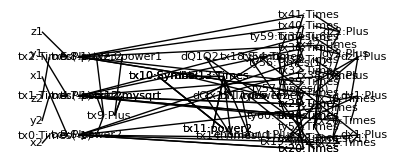

```mathematica
Show[Graphics[gr],AspectRatio->0.41]
```